# Calculating the IGRB contribution of blazars using the LF

## Setting everything up

## Loads in various digitizations and sets some other things up

```mathematica
AppendTo[$Path, NotebookDirectory[]];
<<GCascadeV4.wl
logSpace[start_,end_,num_]:=10^(Range[Log10[start],Log10[end],(Log10[end]-Log10[start])/(num-1)])
AppendTo[$Path, "/Users/matias/Downloads/blazar_data/"];
blazarEGB=Import["known_components/blazar_egb.csv","CSV"]; (* from fig. 3 of ApJ,800,L27 *)
fermiSensitivity= Import["fermiSensitivityQu.csv","CSV"]; (* from fig. 1 of Qu *)

(* this bit below just fixes some discontinuities in the digitized plot *)
fermiSensitivityFuncOld=Interpolation[fermiSensitivity,InterpolationOrder->1];
fermiSensitivityFunc[x_]:=Module[{val},
If[x<2*10^-10,0,
val =Evaluate[fermiSensitivityFuncOld][x];
If[x>1.1*^-8||val>1,1,
val]
]
]
```

You have imported γ-Cascade V4. Setup will take about a minute.

Package located at /Users/matias/Desktop/mathematica/blazar/

## Cosmology stuff

```mathematica
Mpc=3.086*10^24 (*cm in 1 Mpc*);
(*Ωm=0.315;
ΩΛ=0.685;*)
Ωm=0.3;
ΩΛ=0.7;
c=299792.458  km*s^-1;
H0=67.36 km*s^-1;
dH=c/H0 (*Mpc*);
e[z_]:=Sqrt[Ωm*(1+z)^3+ΩΛ]
dΩ=4*Pi;
(*dC[z_]:=dH*Integrate[1/e[z2],{z2,0,z}];*)
dC[z_?NumericQ]:=dH*(-1.140667+1.195229 (1+z) Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ*(1+z)^3])(*Analytic solution to the above integral*)
dA[z_]:=dC[z]/(1+z)
dL[z_?NumericQ]:=dA[z]*(1+z)^2
dVdz[z_?NumericQ]:=dH*((1+z)^2*dA[z]^2)/e[z]*dΩ
```

## This next bit was written by Carlos Blanco. Gets the figures for IGRB and EGB that we will compare to our predictions.

```mathematica
(*Step 1 Import data*)
(* ref: "The spectrum of isotropic diffuse gamma-ray emission between 100 Mev and 820 GeV"*)
rawData=Import["apj504089t3_mrt.txt","Table"];
data = Transpose@rawData[[35;;]];
modelLength = Length[data[[1]]]/3;
modelAdata = data[[;;,;;modelLength]];
modelBdata =data[[;;,modelLength+1;;2*modelLength]];
modelCdata =data[[;;,2*modelLength+1;;3*modelLength]];
```

```mathematica
(*Step 2:Extract relevant columns for energy,fIGRB,fEGB and uncertainties*)
data = modelAdata;

IntToFlux = NIntegrate[x^-2,{x,100,140}]*10^3;

energyLower=data[[2]]*10.^-3 (*Lower bound of energy*);
energyUpper=data[[3]] *10.^-3(*Upper bound of energy*);

fIGRB=IntToFlux*data[[4]]; (*fIGRB values*)
fIGRBUpp=IntToFlux*data[[5]]; (*Upper uncertainty for fIGRB*)
fIGRBLow=IntToFlux*data[[6]]; (*Lower uncertainty for fIGRB*)

fIGRBFgUpp=IntToFlux*data[[7]]; (*Upper uncertainty from foreground modeling*)
fIGRBFgLow=IntToFlux*data[[8]]; (*Lower uncertainty from foreground modeling*)

fEGB=IntToFlux*data[[9]]; (*fEGB values*)
fEGBUpp=IntToFlux*data[[10]]; (*Upper uncertainty for fEGB*)
fEGBLow=IntToFlux*data[[11]]; (*Lower uncertainty for fEGB*)

fEGBFgUpp=IntToFlux*data[[12]]; (*Upper uncertainty from foreground modeling*)
fEGBFgLow=IntToFlux*data[[13]]; (*Lower uncertainty from foreground modeling*)

(*Step 3:Calculate the center of the logarithmic energy bin*)
energyCenter=Sqrt[energyLower*energyUpper];


(*Table 1:Energies with uncertainties*)
energyUncertaintyTable=Around[energyCenter,{energyCenter-energyLower,energyUpper-energyCenter}];

makeUncList[centerList_,lowerList_,upperList_]:=Table[Around[centerList[[i]],{lowerList[[i]],upperList[[i]]}],{i,1,Length@centerList}]

(*Table 2:fIGRB with uncertainties*)
fIGRBTable = makeUncList[fIGRB,fIGRBLow,fIGRBUpp];

(*Table 3:fEGB with uncertainties*)
fEGBTable=makeUncList[fEGB,fEGBLow,fEGBUpp];
```

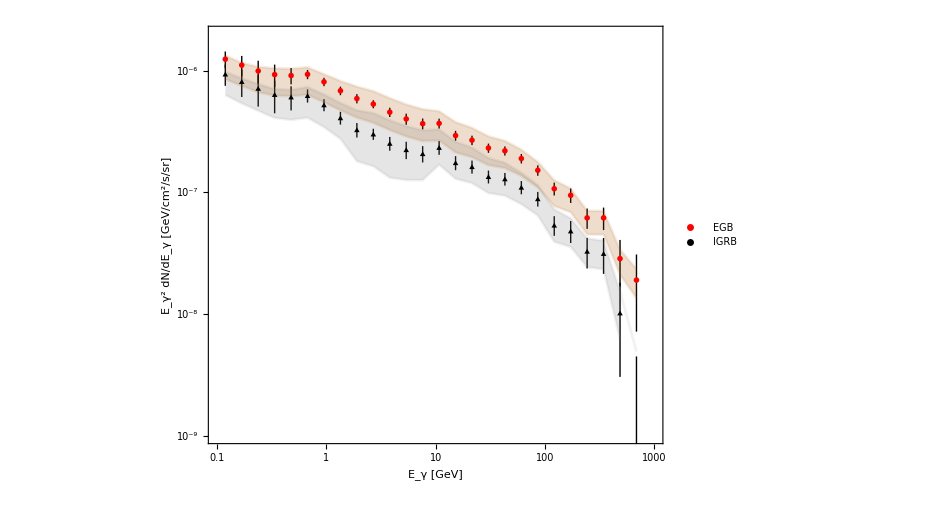

```mathematica
(*Step5: make plotable tables for the models and foreground uncertainty ranges*)
EGBModel = Thread[{energyCenter,energyCenter*fEGBTable}];
EGBForegroundUpper = Thread[{energyCenter,energyCenter*(fEGB+fEGBFgUpp)}];
EGBForegroundLower = Thread[{energyCenter,energyCenter*(fEGB-fEGBFgLow)}];
IGRBModel = Thread[{energyCenter,energyCenter*fIGRBTable}];
IGRBForegroundUpper = Thread[{energyCenter,energyCenter*(fIGRB+fIGRBFgUpp)}];
IGRBForegroundLower = Thread[{energyCenter,energyCenter*(fIGRB-fIGRBFgLow)}];

(*PlotStyle colors*)
EGBPointStyle = {Red};
EGBRangeStyle = {Opacity[0.1],Darker@Orange};
IGRBPointStyle = {Black};
IGRBRangeStyle = {Opacity[0.1],Gray};

(*Step 6:Generate log-log plot*)

plot=ListLogLogPlot[{EGBModel,
EGBForegroundUpper,EGBForegroundLower,IGRBModel,IGRBForegroundUpper,IGRBForegroundLower},
Frame->True,
Joined->{False,True,True,False,True,True},
Filling->{2->{3},5->{6}},
PlotStyle->{EGBPointStyle,EGBRangeStyle,EGBRangeStyle,IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle},
PlotRange->{{10^-1,10^3},{10^-9,2*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,{Automatic,Scaled[0.02]},None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->14],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->14],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
PlotLegends->Placed[{Style["EGB",FontFamily->"Times"],None,None,Style["IGRB",FontFamily->"Times"],None,None},{0.5,0.2}]]
```

## Working out the model of known components

### These known components come from fig. 4 of 2104.03315

```mathematica
SFlowerArr=Import["known_components/SF_lower.csv","CSV"];
SFmidArr=Import["known_components/SF_mid.csv","CSV"];
SFupperArr=Import["known_components/SF_upper.csv","CSV"];
mAGNlowerArr=Import["known_components/mAGN_lower.csv","CSV"];
mAGNmidArr=Import["known_components/mAGN_mid.csv","CSV"];
mAGNupperArr=Import["known_components/mAGN_upper.csv","CSV"];
FSRQlowerArr=Import["known_components/fsrq_lower.csv","CSV"];
FSRQmidArr=Import["known_components/fsrq_mid.csv","CSV"];
FSRQupperArr=Import["known_components/fsrq_upper.csv","CSV"];
LAClowerArr=Import["known_components/bllac_lower.csv","CSV"];
LACmidArr=Import["known_components/bllac_mid.csv","CSV"];
LACupperArr=Import["known_components/bllac_upper.csv","CSV"];
knownMidArr=Import["known_components/all_mid.csv","CSV"];
knownUpperArr=Import["known_components/all_upper.csv","CSV"];
knownLowerArr=Import["known_components/all_lower.csv","CSV"];
```

```mathematica
SFlowerInterp=Interpolation[SFlowerArr];
SFmidInterp=Interpolation[SFmidArr];
SFupperInterp=Interpolation[SFupperArr];
mAGNlowerInterp=Interpolation[mAGNlowerArr];
mAGNmidInterp=Interpolation[mAGNmidArr];
mAGNupperInterp=Interpolation[mAGNupperArr];
FSRQlowerInterp=Interpolation[FSRQlowerArr];
FSRQmidInterp=Interpolation[FSRQmidArr];
FSRQupperInterp=Interpolation[FSRQupperArr];
LAClowerInterp=Interpolation[LAClowerArr];
LACmidInterp=Interpolation[LACmidArr];
LACupperInterp=Interpolation[LACupperArr];
knownMidInterp=Interpolation[knownMidArr];
knownUpperInterp=Interpolation[knownUpperArr];
knownLowerInterp=Interpolation[knownLowerArr];
```

```mathematica
SFlower[x_]:=Piecewise[{
{SFlowerInterp[x],x<=Max[SFlowerArr[[All,1]]]},
{0,x>Max[SFlowerArr[[All,1]]]}
}];
SFmid[x_]:=Piecewise[{
{SFmidInterp[x],x<=Max[SFmidArr[[All,1]]]},
{0,x>Max[SFmidArr[[All,1]]]}
}];
SFupper[x_]:=Piecewise[{
{SFupperInterp[x],x<=Max[SFupperArr[[All,1]]]},
{0,x>Max[SFupperArr[[All,1]]]}
}];
mAGNlower[x_]:=Piecewise[{
{mAGNlowerInterp[x],x<=Max[mAGNlowerArr[[All,1]]]},
{0,x>Max[mAGNlowerArr[[All,1]]]}
}];
mAGNmid[x_]:=Piecewise[{
{mAGNmidInterp[x],x<=Max[mAGNmidArr[[All,1]]]},
{0,x>Max[mAGNmidArr[[All,1]]]}
}];
mAGNupper[x_]:=Piecewise[{
{mAGNupperInterp[x],x<=Max[mAGNupperArr[[All,1]]]},
{0,x>Max[mAGNupperArr[[All,1]]]}
}];
FSRQlower[x_]:=Piecewise[{
{FSRQlowerInterp[x],x<=Max[FSRQlowerArr[[All,1]]]},
{0,x>Max[FSRQlowerArr[[All,1]]]}
}];
FSRQmid[x_]:=Piecewise[{
{FSRQmidInterp[x],x<=Max[FSRQmidArr[[All,1]]]},
{0,x>Max[FSRQmidArr[[All,1]]]}
}];
FSRQupper[x_]:=Piecewise[{
{FSRQupperInterp[x],x<=Max[FSRQupperArr[[All,1]]]},
{0,x>Max[FSRQupperArr[[All,1]]]}
}];
LAClower[x_]:=Piecewise[{
{LAClowerInterp[x],x<=Max[LAClowerArr[[All,1]]]},
{0,x>Max[LAClowerArr[[All,1]]]}
}];
LACmid[x_]:=Piecewise[{
{LACmidInterp[x],x<=Max[LACmidArr[[All,1]]]},
{0,x>Max[LACmidArr[[All,1]]]}
}];
LACupper[x_]:=Piecewise[{
{LACupperInterp[x],x<=Max[LACupperArr[[All,1]]]},
{0,x>Max[LACupperArr[[All,1]]]}
}];
knownMid[x_]:=Piecewise[{
{knownMidInterp[x],x<=Max[knownMidArr[[All,1]]]},
{0,x>Max[knownMidArr[[All,1]]]}
}];
knownUpper[x_]:=Piecewise[{
{knownUpperInterp[x],x<=Max[knownUpperArr[[All,1]]]},
{0,x>Max[knownUpperArr[[All,1]]]}
}];
knownLower[x_]:=Piecewise[{
{knownLowerInterp[x],x<=Max[knownLowerArr[[All,1]]]},
{0,x>Max[knownLowerArr[[All,1]]]}
}];
```

```mathematica
arr=logSpace[0.2,700,1000];
SFmidData=Table[{i,SFmid[i]},{i,arr}];
SFlowerData=Table[{i,SFlower[i]},{i,arr}];
SFupperData=Table[{i,SFupper[i]},{i,arr}];
mAGNmidData=Table[{i,mAGNmid[i]},{i,arr}];
mAGNlowerData=Table[{i,mAGNlower[i]},{i,arr}];
mAGNupperData=Table[{i,mAGNupper[i]},{i,arr}];
FSRQlowerData=Table[{i,FSRQlower[i]},{i,arr}];
FSRQmidData=Table[{i,FSRQmid[i]},{i,arr}];
FSRQupperData=Table[{i,FSRQupper[i]},{i,arr}];
LACmidData=Table[{i,LACmid[i]},{i,arr}];
LAClowerData=Table[{i,LAClower[i]},{i,arr}];
LACupperData=Table[{i,LACupper[i]},{i,arr}];
knownMidData=Table[{i,knownMid[i]},{i,arr}];
knownLowerData=Table[{i,knownLower[i]},{i,arr}];
knownUpperData=Table[{i,knownUpper[i]},{i,arr}];
```

```mathematica
SFmidLog=Log10@SFmidData;
SFupperLog=Log10@SFupperData;
SFlowerLog=Log10@SFlowerData;
mAGNmidLog=Log10@mAGNmidData;
mAGNupperLog=Log10@mAGNupperData;
mAGNlowerLog=Log10@mAGNlowerData;
FSRQupperLog=Log10@FSRQupperData;
FSRQlowerLog=Log10@FSRQlowerData;
FSRQmidLog=Log10@FSRQmidData;
LACupperLog=Log10@LACupperData;
LAClowerLog=Log10@LAClowerData;
LACmidLog=Log10@LACmidData;
knownMidLog=Log10@knownMidData;
```

```mathematica
SFlogDiff=Transpose[{SFupperLog[[All,1]],(SFupperLog[[All,2]]-SFlowerLog[[All,2]])/2}]/.-Infinity->0//Quiet;
mAGNlogDiff=Transpose[{SFupperLog[[All,1]],(mAGNupperLog[[All,2]]-mAGNlowerLog[[All,2]])/2}];
LAClogDiff=Transpose[{SFupperLog[[All,1]],(LACupperLog[[All,2]]-LAClowerLog[[All,2]])/2}];
FSRQlogDiff=Transpose[{SFupperLog[[All,1]],(FSRQupperLog[[All,2]]-FSRQlowerLog[[All,2]])/2}]/.Infinity->0/.Indeterminate->0//Quiet;
```

```mathematica
allError=Transpose[{SFlogDiff[[All,1]],1/(Log[10])*Sqrt[SFlogDiff[[All,2]]^2+mAGNlogDiff[[All,2]]^2+LAClogDiff[[All,2]]^2+FSRQlogDiff[[All,2]]^2]}];
relevantError=Transpose[{SFlogDiff[[All,1]],1/(Log[10])*Sqrt[SFlogDiff[[All,2]]^2+mAGNlogDiff[[All,2]]^2]}];
```

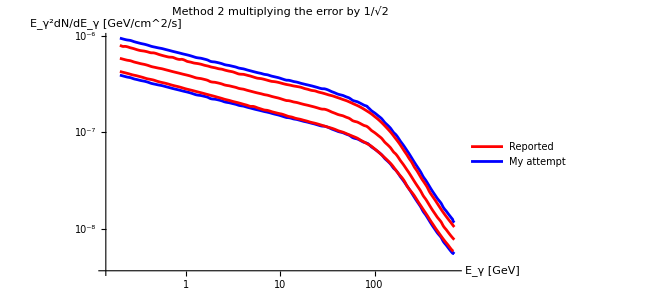

```mathematica
ListLogLogPlot[{knownMidData,Transpose[{10^allError[[All,1]],knownMidData[[All,2]]*10^(1/Sqrt[2*Log@2]*allError[[All,2]])}],Transpose[{10^allError[[All,1]],knownMidData[[All,2]]/10^(1/Sqrt[2]*allError[[All,2]])}],knownUpperData,knownLowerData},Joined->True,PlotRange->All,PlotStyle->{Red,Blue,Blue,Red,Red},PlotLegends->Placed[{"Reported","My attempt"},{0.5,0.2}],AxesLabel->{"E_γ [GeV]","E_γ^2dN/dE_γ [GeV/cm^2/s]"},PlotLabel->"Method 2 multiplying the error by 1/√2"]
```

```mathematica
knownLowerRelevantArr=Transpose[{10^relevantError[[All,1]],(SFmidData[[All,2]]+mAGNmidData[[All,2]])/10^(relevantError[[All,2]]/Sqrt[2])}];
knownLowerRelevantInterp = Interpolation[knownLowerRelevantArr];
knownLowerRelevant[x_]:=Piecewise[{
{knownLowerRelevantInterp[x],x<=Max[knownLowerRelevantArr[[All,1]]]},
{0,x>Max[knownLowerRelevantArr[[All,1]]]}
}]//Quiet;
```

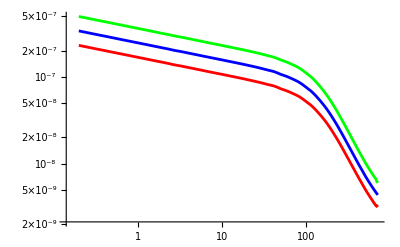

```mathematica
ListLogLogPlot[{knownLowerRelevantArr,Transpose[{10^relevantError[[All,1]],(SFmidData[[All,2]]+mAGNmidData[[All,2]])}],Transpose[{10^relevantError[[All,1]],(SFmidData[[All,2]]+mAGNmidData[[All,2]])*10^(relevantError[[All,2]]/Sqrt[2])}]},PlotStyle->{Red,Blue,Green},Joined->True]
```

## Defining various models and other functions necessary

### γ-ray spectrum models

```mathematica
EbFunc[Γ_]:=10^9.25*10^(-4.11Γ) (* comes from fig. 2 of 1501.0530 *)
(* two spectra. neither include constant (cancels out for L/η) and attenuation (not in L) *)
dNdEPL[En_,Γ_,Ecut_]:=En^-Γ*Exp[-En/Ecut] (* Gev^-Γ (units get fixed by normalization factor) *)
dNdEDPL[En_?NumericQ,Γ_?NumericQ,Ecut_?NumericQ]:=Module[{γa=1.7,γb=2.6},
((En/EbFunc[Γ])^γa+(En/EbFunc[Γ])^γb)^-1* Exp[-En/Ecut] 
] (* This is from eq. 11 of 1501.0530 *)
dNdEnormDPL[En_,Γ_,Ecut_]:=dNdEDPL[En,Γ,Ecut]/NIntegrate[Energy*dNdEDPL[Energy,Γ,Ecut],{Energy,0.1,100}] (* normalizes it so that the normalization factor is just equal to luminosity *)
dNdEarrDPL[Γ_,Ecut_]:=Table[dNdEnormDPL[En,Γ,Ecut],{En,energies}]//Quiet
dNdEnormPL[En_,Γ_,Ecut_]:=dNdEPL[En,Γ,Ecut]/NIntegrate[Energy*dNdEPL[Energy,Γ,Ecut],{Energy,0.1,100}]
dNdEarrPL[Γ_,Ecut_]:=Table[dNdEnormPL[En,Γ,Ecut],{En,energies}]//Quiet
```

### Luminosity functions

```mathematica
ΦPLE[Lext_,Γext_,zext_]:=Module[{A=10^-6.39,γ1=0.62,γ2=1.92,Lstar=10^44.72,kstar=4.23,τ=0.7,ξ=-0.43,μstar=1.93,β=0.066,σ=0.23,μ,kd,evo,Φ0},
μ[L_]:=μstar+β*(Log10[L]-46);
kd[L_]:=kstar+τ*(Log10[L]-46);
evo[L_,z_]:=(1+z)^kd[L]*Exp[z/ξ];
Φ0[L_,Γ_]:=A/(Log[10]*L)*((L/Lstar)^γ1+(L/Lstar)^γ2)^-1*Exp[(-0.5*(Γ-μ[L])^2)/σ^2];
Φ0[Lext/evo[Lext,zext],Γext]
](*Mpc^-3*);

ΦPDE[Lext_,Γext_,zext_]:=Module[{A=10^-6.41,γ1=1.89,γ2=0.72,Lstar=10^44.69,kstar=13.53,τ=1.97,ξ=-0.13,μstar=1.93,β=0.08,σ=0.23,μ,kd,evo,Φ0},
μ[L_]:=μstar+β*(Log10[L]-46);
kd[L_]:=kstar+τ*(Log10[L]-46);
evo[L_,z_]:=(1+z)^kd[L]*Exp[z/ξ];
Φ0[L_,Γ_]:=A/(Log[10]*L)*((L/Lstar)^γ1+(L/Lstar)^γ2)^-1*Exp[(-0.5*(Γ-μ[L])^2)/σ^2];
Φ0[Lext,Γext]*evo[Lext,zext]
] (*Mpc^-3*);

ΦLDDE[Lext_,Γext_,zext_]:=Module[{A=10^-5.32,γ1=1.37,γ2=0.51,Lstar=10^44.28,kstar=4.81,τ=-1.6,p2=-8.27,zcstar=0.94,α=0.14,μstar=1.93,β=0.083,σ=0.23,μ,zc,p1,evo,Φ0},
μ[L_]:=μstar+β*(Log10[L]-46);
zc[L_]:=zcstar*(L/10^48)^α;
p1[L_]:=kstar+τ*(Log10[L]-46);
evo[L_,z_]:=(((1+z)/(1+zc[L]))^p1[L]+((1+z)/(1+zc[L]))^p2)^-1;
Φ0[L_,Γ_]:=A/(Log[10]*L)*((L/Lstar)^γ1+(L/Lstar)^γ2)^-1*Exp[(-0.5*(Γ-μ[L])^2)/σ^2];
Φ0[Lext,Γext]*evo[Lext,zext]
](*Mpc^-3, note that this one might not work since they do not give δ in their paper*);
```

### Flux

```mathematica
(*Ghislenni*)
flux[L_?NumericQ,Γ_?NumericQ,z_?NumericQ,EminGeV_,EmaxGeV_]:=Module[{h=6.62607015*^-27,(*erg s*)nuFactor=2.418*^23,(*Hz/GeV*)α,ν1,ν2,Sγ,Fγ,dLcm},
α=Γ-1;
ν1=EminGeV*nuFactor;
ν2=EmaxGeV*nuFactor;
dLcm=dL[z]*Mpc;
Sγ=L*(1+z)^(1-α)/(4 Pi*dLcm^2);If[α!=1,Fγ=(Sγ*(1-α))/(α*h*ν1*((ν2/ν1)^(1-α)-1)),Fγ=Sγ/(h*ν1*Log[ν2/ν1])];
Fγ]
```

## Now onto the actual calculations

## LDDE

### If you want to load the data from the CSV use the cell below

```mathematica
Γarr = Flatten[ToExpression[Import["/Users/matias/Downloads/flux_arrs/GAMMA_arr.csv","CSV"]]];
EcutArr= Flatten[ToExpression[Import["/Users/matias/Downloads/flux_arrs/Ecut_arr.csv","CSV"]]];
fluxArrLDDEdpl=Delete[ToExpression[Import["/Users/matias/Downloads/flux_arrs/mathematica/ldde_dpl.csv","CSV"]],1];
```

### If you want to do the calculations yourself, evaluate the bit below

```mathematica
ρ[Γ_,z_]:=Mpc^-3*(NIntegrate[Exp[2*L]*Φ[Exp[L],Γ,z],{L,Log[4*^40],Log[10^50]},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->60,PrecisionGoal->Floor[Γ+1]]-NIntegrate[Exp[2*L]*Φ[Exp[L],Γ,z]*fermiSensitivityFunc[flux[Exp[L],Γ,z,0.1,100]],{L,Log[4*^40],Log[10^50]},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->60,PrecisionGoal->Floor[Γ+1]] )//Quiet(* integrand mulitplies by 1-fermi (split it up because it works more nicely), the Floor[Γ] bit just helps the integrator work nicely (higher precision goal is needed for higher spectral indices) *)
ρArr[Γ_]:=ParallelTable[ρ[Γ,z],{z,diffuseDistances}]
cascFunc[Γ_,Ecut_]:=CascadeDiffuse[dNdEarrDPL[Γ,Ecut],10,ρArr[Γ]*624.151]
```

#### DPL

```mathematica
ρ[Γ_,z_]:=Mpc^-3*(NIntegrate[Exp[2*L]*ΦLDDE[Exp[L],Γ,z],{L,Log[4*^40],Log[10^50]},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->60,PrecisionGoal->Floor[Γ+1]]-NIntegrate[Exp[2*L]*ΦLDDE[Exp[L],Γ,z]*fermiSensitivityFunc[flux[Exp[L],Γ,z,0.1,100]],{L,Log[4*^40],Log[10^50]},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->60,PrecisionGoal->Floor[Γ+1]] )//Quiet(* integrand mulitplies by 1-fermi (split it up because it works more nicely), the Floor[Γ] bit just helps the integrator work nicely (higher precision goal is needed for higher spectral indices) *)
ρArr[Γ_]:=ParallelTable[ρ[Γ,z],{z,diffuseDistances}]
cascFunc[Γ_,Ecut_]:=CascadeDiffuse[dNdEarrDPL[Γ,Ecut],10,ρArr[Γ]*624.151]
```

```mathematica
ρArrFull[Γ_,zmax_]:=Table[{z,ρ[Γ,z]},{z,logSpace[10^-6,zmax,128]}]
ρFull1=ρArrFull[1.01,50];
ρFull2=ρArrFull[2.2,50];
ρFull3=ρArrFull[3.5,50];
CloseKernels[];
LaunchKernels[];
```

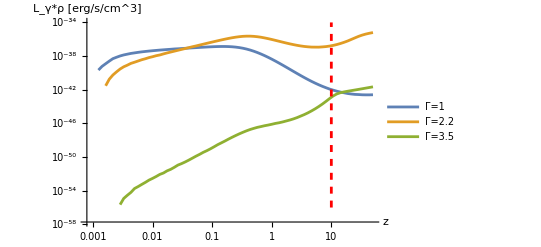

```mathematica
ListLogLogPlot[{ρFull1,ρFull2,ρFull3,Table[{10,i},{i,logSpace[10^-56,10^-34,10]}]},Joined->True,AxesLabel->{"z","L_γ*ρ [erg/s/cm^3]"},PlotStyle->{Automatic,Automatic,Automatic,{Dashed,Red}},PlotLegends->Placed[{"Γ=1","Γ=2.2","Γ=3.5"},Below]]
(* γ-cascade evaluates CascadeDiffuse up until the red dotted line *)
```

```mathematica
arr=logSpace[10^-3,10,64] (* when z<6, dNdz=0*);
ρres0=Transpose[{arr,ParallelTable[ρ[1.01,arr[[i]]],{i,1,Length[arr]}]}];
ρres1=Transpose[{arr,ParallelTable[ρ[1.5,arr[[i]]],{i,1,Length[arr]}]}];
ρres2=Transpose[{arr,ParallelTable[ρ[2,arr[[i]]],{i,1,Length[arr]}]}];
ρres3=Transpose[{arr,ParallelTable[ρ[2.5,arr[[i]]],{i,1,Length[arr]}]}];
ρres4=Transpose[{arr,ParallelTable[ρ[3,arr[[i]]],{i,1,Length[arr]}]}];
ρres5=Transpose[{arr,ParallelTable[ρ[3.5,arr[[i]]],{i,1,Length[arr]}]}];
CloseKernels[];
LaunchKernels[];
```

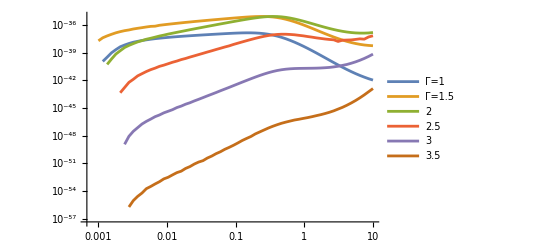

```mathematica
ListLogLogPlot[{ρres0,ρres1,ρres2,ρres3,ρres4,ρres5},Joined->True,PlotLegends->Placed[{"Γ=1","Γ=1.5","2","2.5","3","3.5"},Below]]
```

```mathematica
Γarr =Range[1.01,3,(3-1)/(10-1)];
EcutArr={1000,6000,100000};
fluxArr = Table[
Table[
Transpose[{energies,energies^2*cascFunc[i,j]}],
{i,Γarr}],
{j,EcutArr}];
CloseKernels[];
LaunchKernels[];
```

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

```mathematica
(*fluxArrs=Prepend[fluxArrs,{"Different Ecut (see other csv)","Different Γ (see other csv)","Gamma-Ray Energy [GeV]","Energy^2 * Differential Flux [GeV cm^-2 ^sr-1]"}];*)
fluxArr=Prepend[fluxArr,{"Different Ecut (see other csv)","Different Γ (see other csv)","Gamma-Ray Energy [GeV] (see γ-cascade list)","Energy^2 * Differential Flux [GeV cm^-2 ^sr-1]"}];
Export["/Users/matias/Downloads/flux_arrs.csv",fluxArr];
Export["/Users/matias/Downloads/GAMMA_arr.csv",Γarr];
Export["/Users/matias/Downloads/Ecut_arr.csv",EcutArr];
(*Export["/Users/matias/Downloads/Ecut_arr.csv",EcutArr];*)
fluxArr=Delete[fluxArr,1];
```

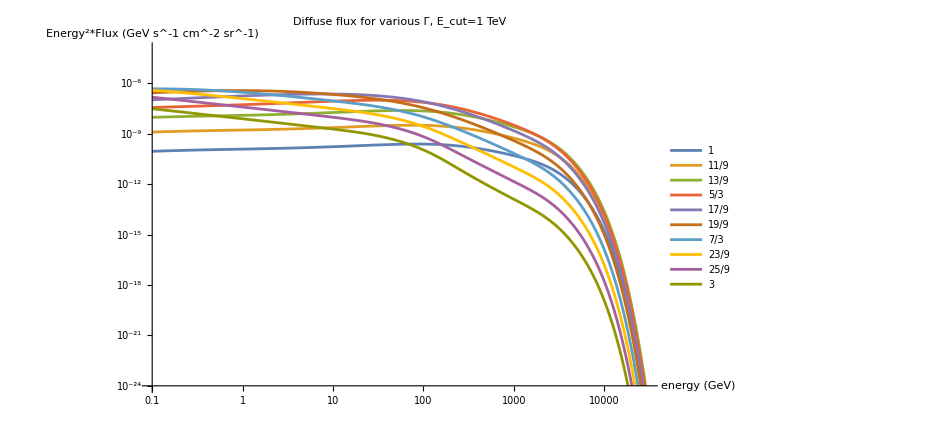

```mathematica
ListLogLogPlot[fluxArr[[1]],Joined->True,PlotRange->{{0.1,30000},{10^-4,10^-24}},AxesLabel->{"energy (GeV)","Energy^2*Flux (GeV s^-1 cm^-2 sr^-1)"},PlotLabel->"Diffuse flux for various Γ, E_cut=1 TeV",PlotLegends->Placed[Γarr,Below]]
```

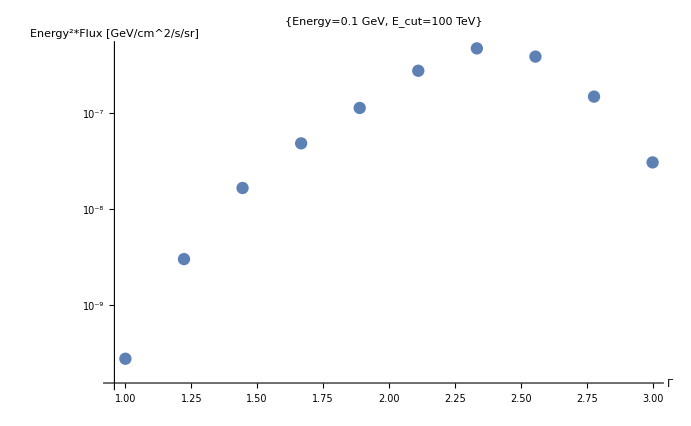

```mathematica
ListLogPlot[Transpose[{Γarr,fluxArr[[3,All,1,2]]}],PlotLabel->{"Energy=0.1 GeV, E_cut=100 TeV"},AxesLabel->{"Γ","Energy^2*Flux [GeV/cm^2/s/sr]"}]
```

### Integrating Γ

```mathematica
Δγ=Γarr[[2]]-Γarr[[1]];
diffuseFluxArrsLDDEdpl=Table[
Transpose[{energies,Sum[(fluxArrLDDEdpl[[j]][[i]][[All,2]]+fluxArrLDDEdpl[[j]][[i+1]][[All,2]])/2*Δγ,{i,Length[Γarr]-1}]}],
{j,3}];
diffuseFluxLDDEdpl=Table[
Interpolation[diffuseFluxArrsLDDEdpl[[i]]],
{i,3}];
```

### Plotting the results

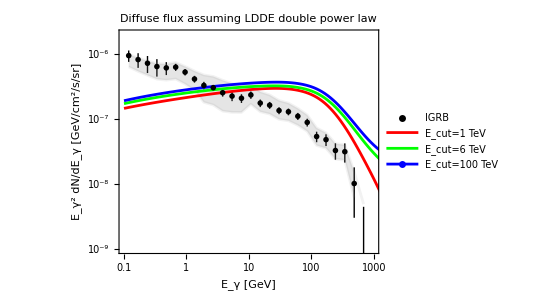

```mathematica
plot=ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,diffuseFluxArrsLDDEdpl[[1]],diffuseFluxArrsLDDEdpl[[2]],diffuseFluxArrsLDDEdpl[[3]]},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green,Blue},
PlotRange->{{10^-1,10^3},{10^-9,2*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->18],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->18],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
ImageSize->{Automatic,400},
PlotLabel->Style["Diffuse flux assuming LDDE double power law",FontFamily->"Times",FontSize->25,Black],
PlotLegends->Placed[{Style["IGRB",FontFamily->"Times",FontSize->14],None,None,
Style["E_cut=1 TeV",FontFamily->"Times",FontSize->14],
Style["E_cut=6 TeV",FontFamily->"Times",FontSize->14],
Style["E_cut=100 TeV",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

#### Taking into account the model of known contributions

```mathematica
knownPlus1=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsLDDEdpl[[1]][[All,2]],100]}];
knownPlus6=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsLDDEdpl[[2]][[All,2]],100]}];
knownPlus100=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsLDDEdpl[[3]][[All,2]],100]}];
```

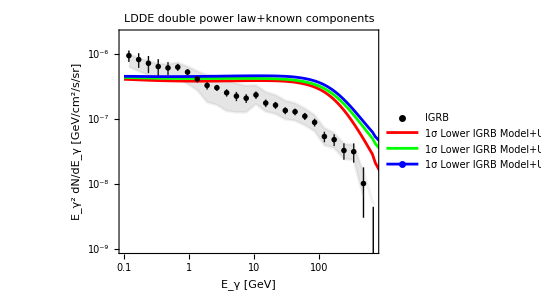

```mathematica
ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,knownPlus1,knownPlus6,knownPlus100},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green,Blue},
PlotRange->{{10^-1,700},{10^-9,2*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->18],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->18],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
ImageSize->{Automatic,400},
PlotLabel->Style["LDDE double power law+known components",FontFamily->"Times",FontSize->25,Black],
PlotLegends->Placed[{
Style["IGRB",FontFamily->"Times",FontSize->14],None,None,Style["1σ Lower IGRB Model+Unresolved Blazars (E_cut=1 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model+Unresolved Blazars (E_cut=6 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model+Unresolved Blazars (E_cut=100 TeV)",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

### Trying it all using a broken power law instead of a broken double power law

#### If you want to load it from a CSV use the cell below

```mathematica
Γarr = Flatten[ToExpression[Import["/Users/matias/Downloads/flux_arrs/GAMMA_arr.csv","CSV"]]];
EcutArr= Flatten[ToExpression[Import["/Users/matias/Downloads/flux_arrs/Ecut_arr.csv","CSV"]]];
fluxArrLDDEpl=Delete[ToExpression[Import["/Users/matias/Downloads/flux_arrs/mathematica/ldde_pl.csv","CSV"]],1];
```

#### If you want to do the calculations yourself do the bit below

```mathematica
cascFuncPL[Γ_,Ecut_]:=CascadeDiffuse[dNdEarrPL[Γ,Ecut],10,ρArr[Γ]*624.151]
```

```mathematica
Γarr =Range[1.01,3,(3-1)/(10-1)];
EcutArr={1000,6000,100000};
fluxArrPL = Table[
Table[
Transpose[{energies,energies^2*cascFuncPL[i,j]}],
{i,Γarr}],
{j,EcutArr}];
CloseKernels[];
LaunchKernels[];
```

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

```mathematica
fluxArrPL=Prepend[fluxArrPL,{"Different Ecut (see other csv)","Different Γ (see other csv)","Gamma-Ray Energy [GeV] (see γ-cascade list)","Energy^2 * Differential Flux [GeV cm^-2 ^sr-1]"}];
Export["/Users/matias/Downloads/flux_arrs_pl.csv",fluxArrPL];
```

```mathematica
fluxArrPL=Delete[fluxArrPL,1];
```

#### Integrating Γ

```mathematica
Δγ=Γarr[[2]]-Γarr[[1]];
diffuseFluxArrsLDDEpl=Table[
Transpose[{energies,Sum[(fluxArrLDDEpl[[j]][[i]][[All,2]]+fluxArrLDDEpl[[j]][[i+1]][[All,2]])/2*Δγ,{i,Length[Γarr]-1}]}],
{j,3}];
diffuseFluxLDDEpl=Table[
Interpolation[diffuseFluxArrsLDDEpl[[i]]],
{i,3}];
```

#### Plotting the results

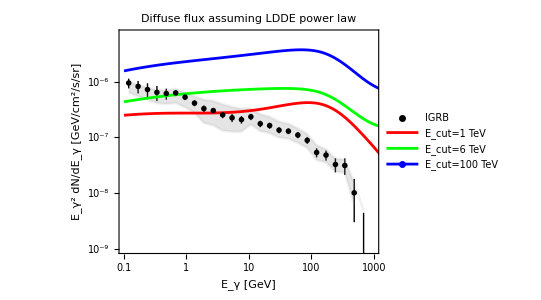

```mathematica
plot=ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,diffuseFluxArrsLDDEpl[[1]],diffuseFluxArrsLDDEpl[[2]],diffuseFluxArrsLDDEpl[[3]]},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green,Blue},
PlotRange->{{10^-1,10^3},{10^-9,7*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->18],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->18],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
ImageSize->{Automatic,400},
PlotLabel->Style["Diffuse flux assuming LDDE power law",FontFamily->"Times",FontSize->25,Black],
PlotLegends->Placed[{Style["IGRB",FontFamily->"Times",FontSize->14],None,None,
Style["E_cut=1 TeV",FontFamily->"Times",FontSize->14],
Style["E_cut=6 TeV",FontFamily->"Times",FontSize->14],
Style["E_cut=100 TeV",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

#### Taking into account the model of known contributions

```mathematica
knownPlus1PL=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsLDDEpl[[1]][[All,2]],100]}];
knownPlus6PL=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsLDDEpl[[2]][[All,2]],100]}];
knownPlus100PL=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsLDDEpl[[3]][[All,2]],100]}];
```

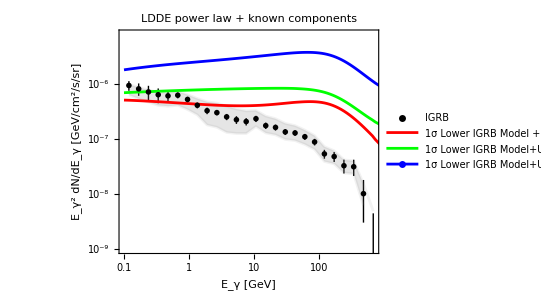

```mathematica
ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,knownPlus1PL,knownPlus6PL,knownPlus100PL},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green,Blue},
PlotRange->{{10^-1,700},{10^-9,8*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->18],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->18],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
PlotLabel->Style["LDDE power law + known components",FontFamily->"Times",FontSize->25,Black],
ImageSize->{Automatic,400},
PlotLegends->Placed[{
Style["IGRB",FontFamily->"Times",FontSize->14],None,None,Style["1σ Lower IGRB Model +Unresolved Blazars (E_cut=1 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model+Unresolved Blazars (E_cut=6 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model+Unresolved Blazars (E_cut=100 TeV)",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

## PLE

### If you want to load in the calculations from a CSV run the cell below

```mathematica
Γarr = Flatten[ToExpression[Import["/Users/matias/Downloads/flux_arrs/GAMMA_arr.csv","CSV"]]];
EcutArr= Flatten[ToExpression[Import["/Users/matias/Downloads/flux_arrs/Ecut_arr.csv","CSV"]]];
fluxArrPLEdpl=Delete[ToExpression[Import["/Users/matias/Downloads/flux_arrs/mathematica/ple_dpl.csv","CSV"]],1];
fluxArrPLEpl=Delete[ToExpression[Import["/Users/matias/Downloads/flux_arrs/mathematica/ple_pl.csv","CSV"]],1];
```

### If you want to do the calculations run them below

#### First with a double broken power law

```mathematica
ρPLE[Γ_,z_]:=Mpc^-3*(NIntegrate[Exp[2*L]*ΦPLE[Exp[L],Γ,z],{L,Log[4*^40],Log[10^50]},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->60,PrecisionGoal->Floor[Γ+1]]-NIntegrate[Exp[2*L]*ΦPLE[Exp[L],Γ,z]*fermiSensitivityFunc[flux[Exp[L],Γ,z,0.1,100]],{L,Log[4*^40],Log[10^50]},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->60,PrecisionGoal->Floor[Γ+1]] )//Quiet(* integrand mulitplies by 1-fermi (split it up because it works more nicely), the Floor[Γ] bit just helps the integrator work nicely (higher precision goal is needed for higher spectral indices) *)
ρArrPLE[Γ_]:=ParallelTable[ρPLE[Γ,z],{z,diffuseDistances}]
cascFuncPLE[Γ_,Ecut_]:=CascadeDiffuse[dNdEarrDPL[Γ,Ecut],10,ρArrPLE[Γ]*624.151]
```

```mathematica
arr=logSpace[10^-3,10,64] (* when z<6, dNdz=0*);
ρres0=Transpose[{arr,ParallelTable[ρPLE[1.01,arr[[i]]],{i,1,Length[arr]}]}];
ρres1=Transpose[{arr,ParallelTable[ρPLE[1.5,arr[[i]]],{i,1,Length[arr]}]}];
ρres2=Transpose[{arr,ParallelTable[ρPLE[2,arr[[i]]],{i,1,Length[arr]}]}];
ρres3=Transpose[{arr,ParallelTable[ρPLE[2.5,arr[[i]]],{i,1,Length[arr]}]}];
ρres4=Transpose[{arr,ParallelTable[ρPLE[3,arr[[i]]],{i,1,Length[arr]}]}];
ρres5=Transpose[{arr,ParallelTable[ρPLE[3.5,arr[[i]]],{i,1,Length[arr]}]}];
CloseKernels[];
LaunchKernels[];
```

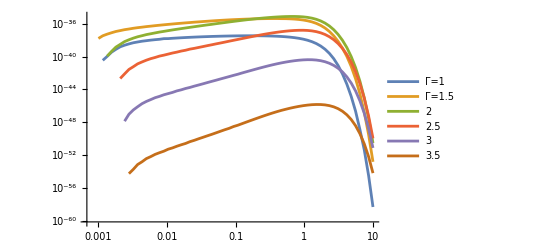

```mathematica
ListLogLogPlot[{ρres0,ρres1,ρres2,ρres3,ρres4,ρres5},Joined->True,PlotLegends->Placed[{"Γ=1","Γ=1.5","2","2.5","3","3.5"},Below]]
```

```mathematica
Γarr =Range[1.01,3,(3-1)/(10-1)];
EcutArr={1000,6000,100000};
fluxArrPLE = Table[
Table[
Transpose[{energies,energies^2*cascFuncPLE[i,j]}],
{i,Γarr}],
{j,EcutArr}];
CloseKernels[];
LaunchKernels[];
```

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

```mathematica
fluxArrPLE=Prepend[fluxArrPLE,{"Different Ecut (see other csv)","Different Γ (see other csv)","Gamma-Ray Energy [GeV] (see γ-cascade list)","Energy^2 * Differential Flux [GeV cm^-2 ^sr-1]"}];
Export["/Users/matias/Downloads/flux_arrs_ple_dpl.csv",fluxArrPLE];
fluxArrPLE=Delete[fluxArrPLE,1];
```

#### Next with a broken power law

```mathematica
cascFuncPLEpl[Γ_,Ecut_]:=CascadeDiffuse[dNdEarrPL[Γ,Ecut],10,ρArrPLE[Γ]*624.151]
```

```mathematica
Γarr =Range[1.01,3,(3-1)/(10-1)];
EcutArr={1000,6000,100000};
fluxArrPLEpl = Table[
Table[
Transpose[{energies,energies^2*cascFuncPLEpl[i,j]}],
{i,Γarr}],
{j,EcutArr}];
CloseKernels[];
LaunchKernels[];
```

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

```mathematica
fluxArrPLEpl=Prepend[fluxArrPLEpl,{"Different Ecut (see other csv)","Different Γ (see other csv)","Gamma-Ray Energy [GeV] (see γ-cascade list)","Energy^2 * Differential Flux [GeV cm^-2 ^sr-1]"}];
Export["/Users/matias/Downloads/flux_arrs_ple_pl.csv",fluxArrPLEpl];
fluxArrPLEpl=Delete[fluxArrPLEpl,1];
```

### Integrating Γ

```mathematica
Δγ=Γarr[[2]]-Γarr[[1]];
diffuseFluxArrsPLEdpl=Table[
Transpose[{energies,Sum[(fluxArrPLEdpl[[j]][[i]][[All,2]]+fluxArrPLEdpl[[j]][[i+1]][[All,2]])/2*Δγ,{i,Length[Γarr]-1}]}],
{j,3}];
diffuseFluxPLEdpl=Table[
Interpolation[diffuseFluxArrsPLEdpl[[i]]],
{i,3}];
diffuseFluxArrsPLEpl=Table[
Transpose[{energies,Sum[(fluxArrPLEpl[[j]][[i]][[All,2]]+fluxArrPLEpl[[j]][[i+1]][[All,2]])/2*Δγ,{i,Length[Γarr]-1}]}],
{j,3}];
diffuseFluxPLEpl=Table[
Interpolation[diffuseFluxArrsPLEpl[[i]]],
{i,3}];
```

### Plotting the results

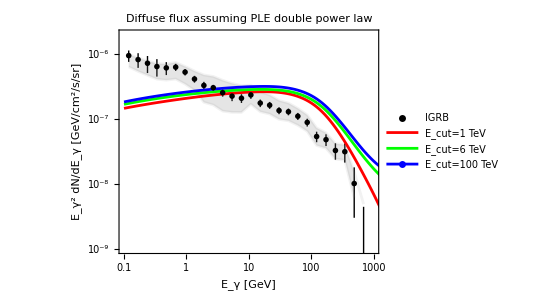

```mathematica
plot=ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,diffuseFluxArrsPLEdpl[[1]],diffuseFluxArrsPLEdpl[[2]],diffuseFluxArrsPLEdpl[[3]]},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green,Blue},
PlotRange->{{10^-1,10^3},{10^-9,2*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->18],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->18],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
ImageSize->{Automatic,400},
PlotLabel->Style["Diffuse flux assuming PLE double power law",FontFamily->"Times",FontSize->25,Black],
PlotLegends->Placed[{Style["IGRB",FontFamily->"Times",FontSize->14],None,None,
Style["E_cut=1 TeV",FontFamily->"Times",FontSize->14],
Style["E_cut=6 TeV",FontFamily->"Times",FontSize->14],
Style["E_cut=100 TeV",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

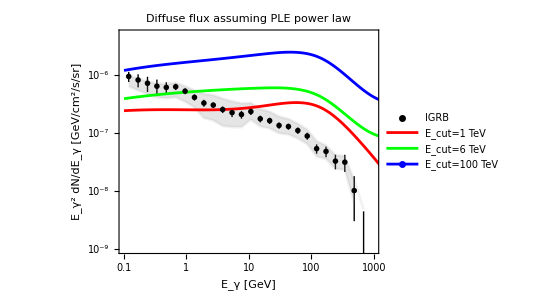

```mathematica
plot=ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,diffuseFluxArrsPLEpl[[1]],diffuseFluxArrsPLEpl[[2]],diffuseFluxArrsPLEpl[[3]]},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green,Blue},
PlotRange->{{10^-1,10^3},{10^-9,5*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->18],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->18],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
ImageSize->{Automatic,400},
PlotLabel->Style["Diffuse flux assuming PLE power law",FontFamily->"Times",FontSize->25,Black],
PlotLegends->Placed[{Style["IGRB",FontFamily->"Times",FontSize->14],None,None,
Style["E_cut=1 TeV",FontFamily->"Times",FontSize->14],
Style["E_cut=6 TeV",FontFamily->"Times",FontSize->14],
Style["E_cut=100 TeV",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

#### Taking into account the model of known contributions

```mathematica
knownPlus1PLEdpl=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPLEdpl[[1]][[All,2]],100]}];
knownPlus6PLEdpl=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPLEdpl[[2]][[All,2]],100]}];
knownPlus100PLEdpl=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPLEdpl[[3]][[All,2]],100]}];
knownPlus1PLEpl=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPLEpl[[1]][[All,2]],100]}];
knownPlus6PLEpl=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPLEpl[[2]][[All,2]],100]}];
knownPlus100PLEpl=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPLEpl[[3]][[All,2]],100]}];
```

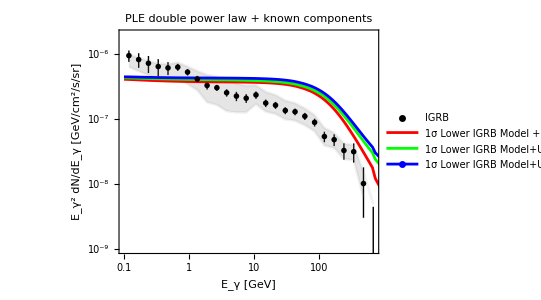

```mathematica
ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,knownPlus1PLEdpl,knownPlus6PLEdpl,knownPlus100PLEdpl},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green,Blue},
PlotRange->{{10^-1,700},{10^-9,2*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->18],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->18],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
PlotLabel->Style["PLE double power law + known components",FontFamily->"Times",FontSize->25,Black],
ImageSize->{Automatic,400},
PlotLegends->Placed[{
Style["IGRB",FontFamily->"Times",FontSize->14],None,None,Style["1σ Lower IGRB Model +Unresolved Blazars (E_cut=1 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model+Unresolved Blazars (E_cut=6 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model+Unresolved Blazars (E_cut=100 TeV)",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

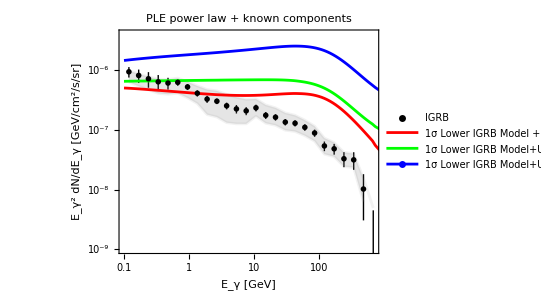

```mathematica
ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,knownPlus1PLEpl,knownPlus6PLEpl,knownPlus100PLEpl},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green,Blue},
PlotRange->{{10^-1,700},{10^-9,4*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->18],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->18],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
PlotLabel->Style["PLE power law + known components",FontFamily->"Times",FontSize->25,Black],
ImageSize->{Automatic,400},
PlotLegends->Placed[{
Style["IGRB",FontFamily->"Times",FontSize->14],None,None,Style["1σ Lower IGRB Model +Unresolved Blazars (E_cut=1 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model+Unresolved Blazars (E_cut=6 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model+Unresolved Blazars (E_cut=100 TeV)",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

## PDE

### If you want to load in the calculations from a CSV run the cell below

```mathematica
Γarr = Flatten[ToExpression[Import["/Users/matias/Downloads/flux_arrs/GAMMA_arr.csv","CSV"]]];
EcutArr= Flatten[ToExpression[Import["/Users/matias/Downloads/flux_arrs/Ecut_arr.csv","CSV"]]];
fluxArrPDEdpl=Delete[ToExpression[Import["/Users/matias/Downloads/flux_arrs/mathematica/pde_dpl.csv","CSV"]],1];
fluxArrPDEpl=Delete[ToExpression[Import["/Users/matias/Downloads/flux_arrs/mathematica/pde_pl.csv","CSV"]],1];
```

### If you want to do the calculations run them below

#### First with a double broken power law

```mathematica
ρPDE[Γ_,z_]:=Mpc^-3*(NIntegrate[Exp[2*L]*ΦPDE[Exp[L],Γ,z],{L,Log[4*^40],Log[10^50]},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->60,PrecisionGoal->Floor[Γ+1]]-NIntegrate[Exp[2*L]*ΦPDE[Exp[L],Γ,z]*fermiSensitivityFunc[flux[Exp[L],Γ,z,0.1,100]],{L,Log[4*^40],Log[10^50]},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->60,PrecisionGoal->Floor[Γ+1]] )//Quiet(* integrand mulitplies by 1-fermi (split it up because it works more nicely), the Floor[Γ] bit just helps the integrator work nicely (higher precision goal is needed for higher spectral indices) *)
ρArrPDE[Γ_]:=ParallelTable[ρPDE[Γ,z],{z,diffuseDistances}]
cascFuncPDE[Γ_,Ecut_]:=CascadeDiffuse[dNdEarrDPL[Γ,Ecut],10,ρArrPDE[Γ]*624.151]
```

```mathematica
Γarr =Range[1.01,3,(3-1)/(10-1)];
EcutArr={1000,6000,100000};
fluxArrPDE = Table[
Table[
Transpose[{energies,energies^2*cascFuncPDE[i,j]}],
{i,Γarr}],
{j,EcutArr}];
CloseKernels[];
LaunchKernels[];
```

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

```mathematica
fluxArrPDE=Prepend[fluxArrPDE,{"Different Ecut (see other csv)","Different Γ (see other csv)","Gamma-Ray Energy [GeV] (see γ-cascade list)","Energy^2 * Differential Flux [GeV cm^-2 ^sr-1]"}];
Export["/Users/matias/Downloads/flux_arrs_pde_dpl.csv",fluxArrPDE];
fluxArrPDE=Delete[fluxArrPDE,1];
```

#### Next with a broken power law

```mathematica
cascFuncPDEpl[Γ_,Ecut_]:=CascadeDiffuse[dNdEarrPL[Γ,Ecut],10,ρArrPDE[Γ]*624.151]
```

```mathematica
Γarr =Range[1.01,3,(3-1)/(10-1)];
EcutArr={1000,6000,100000};
fluxArrPDEpl = Table[
Table[
Transpose[{energies,energies^2*cascFuncPDEpl[i,j]}],
{i,Γarr}],
{j,EcutArr}];
CloseKernels[];
LaunchKernels[];
```

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

```mathematica
fluxArrPDEpl=Prepend[fluxArrPDEpl,{"Different Ecut (see other csv)","Different Γ (see other csv)","Gamma-Ray Energy [GeV] (see γ-cascade list)","Energy^2 * Differential Flux [GeV cm^-2 ^sr-1]"}];
Export["/Users/matias/Downloads/flux_arrs_pde_pl.csv",fluxArrPDEpl];
fluxArrPDEpl=Delete[fluxArrPDEpl,1];
```

### Integrating Γ

```mathematica
Δγ=Γarr[[2]]-Γarr[[1]];
diffuseFluxArrsPDEdpl=Table[
Transpose[{energies,Sum[(fluxArrPDEdpl[[j]][[i]][[All,2]]+fluxArrPDEdpl[[j]][[i+1]][[All,2]])/2*Δγ,{i,Length[Γarr]-1}]}],
{j,3}];
diffuseFluxPDEdpl=Table[
Interpolation[diffuseFluxArrsPDEdpl[[i]]],
{i,3}];
diffuseFluxArrsPDEpl=Table[
Transpose[{energies,Sum[(fluxArrPDEpl[[j]][[i]][[All,2]]+fluxArrPDEpl[[j]][[i+1]][[All,2]])/2*Δγ,{i,Length[Γarr]-1}]}],
{j,3}];
diffuseFluxPDEpl=Table[
Interpolation[diffuseFluxArrsPDEpl[[i]]],
{i,3}];
```

### Plotting the results

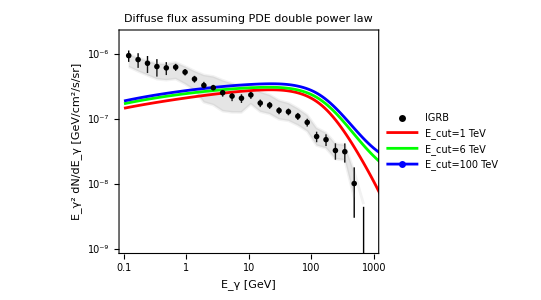

```mathematica
plot=ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,diffuseFluxArrsPDEdpl[[1]],diffuseFluxArrsPDEdpl[[2]],diffuseFluxArrsPDEdpl[[3]]},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green,Blue},
PlotRange->{{10^-1,10^3},{10^-9,2*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->18],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->18],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
ImageSize->{Automatic,400},
PlotLabel->Style["Diffuse flux assuming PDE double power law",FontFamily->"Times",FontSize->25,Black],
PlotLegends->Placed[{Style["IGRB",FontFamily->"Times",FontSize->14],None,None,Style["E_cut=1 TeV",FontFamily->"Times",FontSize->14],Style["E_cut=6 TeV",FontFamily->"Times",FontSize->14],Style["E_cut=100 TeV",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

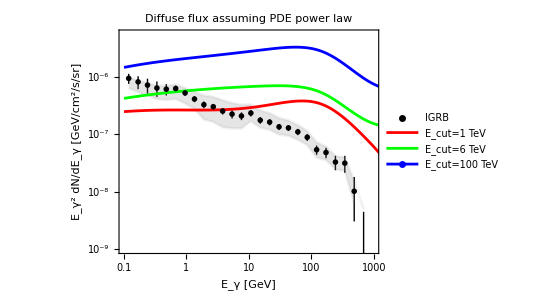

```mathematica
plot=ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,diffuseFluxArrsPDEpl[[1]],diffuseFluxArrsPDEpl[[2]],diffuseFluxArrsPDEpl[[3]]},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green,Blue},
PlotRange->{{10^-1,10^3},{10^-9,5.5*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->18],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->18],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
ImageSize->{Automatic,400},
PlotLabel->Style["Diffuse flux assuming PDE power law",FontFamily->"Times",FontSize->25,Black],
PlotLegends->Placed[{Style["IGRB",FontFamily->"Times",FontSize->14],None,None,
Style["E_cut=1 TeV",FontFamily->"Times",FontSize->14],Style["E_cut=6 TeV",FontFamily->"Times",FontSize->14],
Style["E_cut=100 TeV",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

#### Taking into account the model of known contributions

```mathematica
knownPlus1PDEdpl=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPDEdpl[[1]][[All,2]],100]}];
knownPlus6PDEdpl=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPDEdpl[[2]][[All,2]],100]}];
knownPlus100PDEdpl=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPDEdpl[[3]][[All,2]],100]}];
knownPlus1PDEpl=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPDEpl[[1]][[All,2]],100]}];
knownPlus6PDEpl=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPDEpl[[2]][[All,2]],100]}];
knownPlus100PDEpl=Transpose[{Take[energies,100],Table[knownLowerRelevant[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPDEpl[[3]][[All,2]],100]}];
```

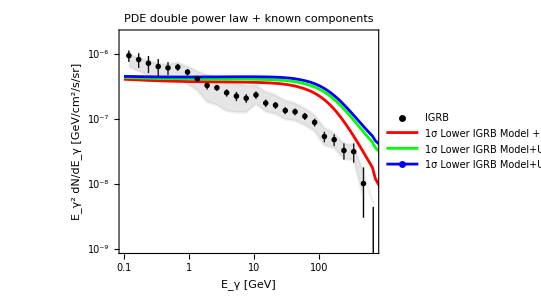

```mathematica
ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,knownPlus1PLEdpl,knownPlus6PDEdpl,knownPlus100PDEdpl},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green,Blue},
PlotRange->{{10^-1,700},{10^-9,2*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->18],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->18],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
PlotLabel->Style["PDE double power law + known components",FontFamily->"Times",FontSize->25,Black],
ImageSize->{Automatic,400},
PlotLegends->Placed[{
Style["IGRB",FontFamily->"Times",FontSize->14],None,None,Style["1σ Lower IGRB Model +Unresolved Blazars (E_cut=1 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model+Unresolved Blazars (E_cut=6 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model+Unresolved Blazars (E_cut=100 TeV)",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

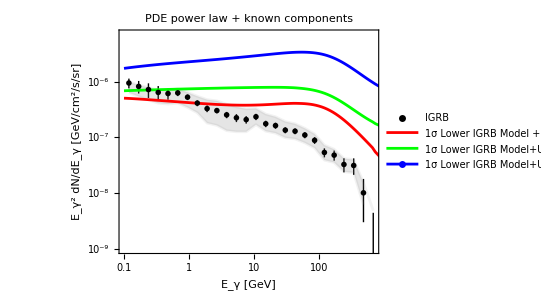

```mathematica
ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,knownPlus1PLEpl,knownPlus6PDEpl,knownPlus100PDEpl},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green,Blue},
PlotRange->{{10^-1,700},{10^-9,7*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->18],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->18],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
PlotLabel->Style["PDE power law + known components",FontFamily->"Times",FontSize->25,Black],
ImageSize->{Automatic,400},
PlotLegends->Placed[{
Style["IGRB",FontFamily->"Times",FontSize->14],None,None,Style["1σ Lower IGRB Model +Unresolved Blazars (E_cut=1 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model+Unresolved Blazars (E_cut=6 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model+Unresolved Blazars (E_cut=100 TeV)",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

## Calculating everything for the resolved blazars

### If you want to load in the values run this cell

```mathematica
Γarr = Flatten[ToExpression[Import["flux_arrs/GAMMA_arr.csv","CSV"]]];
EcutArr= Flatten[ToExpression[Import["flux_arrs/Ecut_arr.csv","CSV"]]];
fluxArrResolved=Delete[ToExpression[Import["flux_arrs/resolved_ldde_pl.csv","CSV"]],1];
LOSfluxArrResolved=Delete[ToExpression[Import["flux_arrs/los_resolved_ldde_pl.csv","CSV"]],1];
```

### If you want to do the calculations yourself run the bit below

```mathematica
ρResolved[Γ_,z_,Ecut_]:=Abs[NIntegrate[L*ΦLDDE[L,Γ,z]*Re[newFermiFunc[fluxPL[L,Γ,z,Ecut]]],{L,10^43,10^52},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->60,PrecisionGoal->(Floor[Γ]+1)] ]//Quiet
ρResolvedArr[Γ_,Ecut_]:=ParallelTable[ρResolved[Γ,z,Ecut],{z,diffuseDistances}]
cascFuncResolved[Γ_,Ecut_]:=CascadeDiffuse[dNdEarrPL[Γ,Ecut],10,ρResolvedArr[Γ,Ecut]*624.151]
attenFuncResolved[Γ_,Ecut_]:=AttenuateDiffuse[dNdEarrPL[Γ,Ecut],10,ρResolvedArr[Γ,Ecut]*624.151]
```

```mathematica
ρArrFull[Γ_,Ecut_,zmax_]:=ParallelTable[{z,ρResolved[Γ,z,Ecut]},{z,logSpace[10^-6,zmax,16]}]
ρFull1=ρArrFull[1,6000,10];
ρFull2=ρArrFull[2.2,6000,10];
ρFull3=ρArrFull[3.5,6000,10];
CloseKernels[];
LaunchKernels[];
```

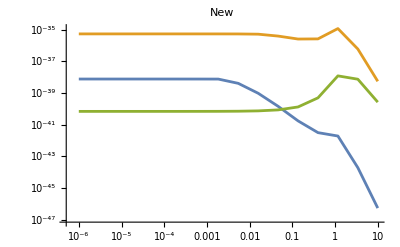

```mathematica
ListLogLogPlot[{ρFull1,ρFull2,ρFull3},Joined->True,PlotLabel->"New"]
```

```mathematica
Γarr =Range[1,3,(3-1)/(10-1)];
EcutArr={1000,6000,100000};
fluxArrResolved = Table[
Table[
Transpose[{energies,energies^2*cascFuncResolved[i,j]}],
{i,Γarr}],
{j,EcutArr}];
CloseKernels[];
LaunchKernels[];
```

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

```mathematica
fluxArrResolved=Prepend[fluxArrResolved,{"Different Ecut (see other csv)","Different Γ (see other csv)","Gamma-Ray Energy [GeV] (see γ-cascade list)","Energy^2 * Differential Flux [GeV cm^-2 ^sr-1]"}];
Export["/Users/matias/Downloads/flux_arrs_resolved.csv",fluxArrResolved];
fluxArrResolved=Delete[fluxArrResolved,1];
```

#### Finding the line of sight contribution (have to subtract it out)

```mathematica
Γarr =Range[1,3,(3-1)/(10-1)];
EcutArr={1000,6000,100000};
LOSresolved = Table[
Table[
Transpose[{energies,energies^2*attenFuncResolved[i,j]}],
{i,Γarr}],
{j,EcutArr}];
CloseKernels[];
LaunchKernels[];
```

$Aborted

### Integrating Γ

```mathematica
Δγ=Γarr[[2]]-Γarr[[1]];
diffuseFluxArrsResolved=Table[
Transpose[{energies,Sum[(fluxArrResolved[[j]][[i]][[All,2]]+fluxArrResolved[[j]][[i+1]][[All,2]])/2*Δγ,{i,9}]}],
{j,3}];
diffuseResolvedFlux=Table[
Interpolation[diffuseFluxArrsResolved[[i]]],
{i,3}];

LOSdiffuseFluxArrsResolved=Table[
Transpose[{energies,Sum[(LOSfluxArrResolved[[j]][[i]][[All,2]]+LOSfluxArrResolved[[j]][[i+1]][[All,2]])/2*Δγ,{i,9}]}],
{j,3}];
LOSdiffuseResolvedFlux=Table[
Interpolation[LOSdiffuseFluxArrsResolved[[i]]],
{i,3}];
```

### Plotting this

```mathematica
resolvedDiffuseCascades=Import["resolved_diffuse_cascades.csv"] (* fig 2 of 2303.01524 *);
```

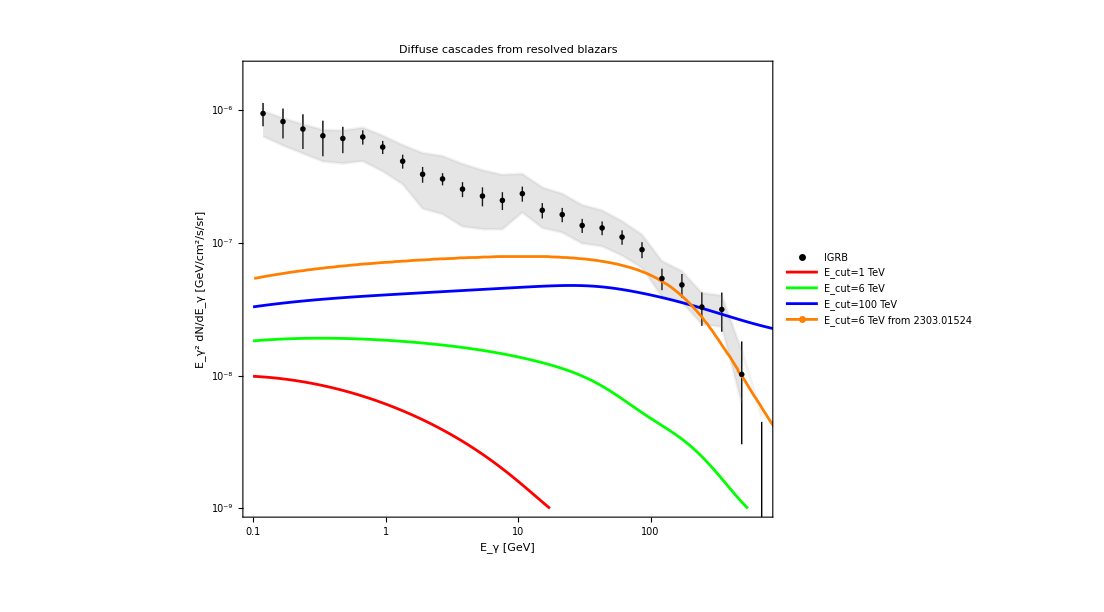

```mathematica
ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,Transpose[{LOSdiffuseFluxArrsResolved[[1]][[All,1]],diffuseFluxArrsResolved[[1]][[All,2]]-LOSdiffuseFluxArrsResolved[[1]][[All,2]]}],Transpose[{LOSdiffuseFluxArrsResolved[[2]][[All,1]],diffuseFluxArrsResolved[[2]][[All,2]]-LOSdiffuseFluxArrsResolved[[2]][[All,2]]}],
Transpose[{LOSdiffuseFluxArrsResolved[[3]][[All,1]],diffuseFluxArrsResolved[[3]][[All,2]]-LOSdiffuseFluxArrsResolved[[3]][[All,2]]}],
resolvedDiffuseCascades},
Frame->True,
Joined->{False,True,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green,Blue,Orange},
PlotRange->{{10^-1,700},{10^-9,2*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->25],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->25],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
PlotLabel->Style["Diffuse cascades from resolved blazars",FontFamily->"Times",FontSize->30,Black],
PlotLegends->Placed[{Style["IGRB",FontFamily->"Times",FontSize->20],None,None,
Style["E_cut=1 TeV",FontFamily->"Times",FontSize->20],
Style["E_cut=6 TeV",FontFamily->"Times",FontSize->20],
Style["E_cut=100 TeV",FontFamily->"Times",FontSize->20],
Style["E_cut=6 TeV from 2303.01524",FontFamily->"Times",FontSize->20]},{.82,.82}]]
```

## Subtracting line of sight, other calculation was causing too much trouble, this way is slower

### Run this cell to load in the lists

```mathematica
LOSfluxArr = Delete[ToExpression[Import["flux_arrs/los_ldde_dpl.csv","CSV"]],1];
LOSfluxArrPL= Delete[ToExpression[Import["flux_arrs/los_ldde_pl.csv","CSV"]],1];
LOSfluxArrPLE=Delete[ToExpression[Import["flux_arrs/los_ple_dpl.csv","CSV"]],1];
LOSfluxArrPLEpl=Delete[ToExpression[Import["flux_arrs/los_ple_pl.csv","CSV"]],1];
```

### Run this cell to do this calculations

```mathematica
attenFunc[Γ_,Ecut_]:=AttenuateDiffuse[dNdEarr[Γ,Ecut],10,ρArr[Γ,Ecut]*624.151]
attenFuncPL[Γ_,Ecut_]:=AttenuateDiffuse[dNdEarrPL[Γ,Ecut],10,ρArrPL[Γ,Ecut]*624.151]
attenFuncPLE[Γ_,Ecut_]:=AttenuateDiffuse[dNdEarr[Γ,Ecut],10,ρPLEArr[Γ,Ecut]*624.151]
attenFuncPLEpl[Γ_,Ecut_]:=AttenuateDiffuse[dNdEarrPL[Γ,Ecut],10,ρPLEArr[Γ,Ecut]*624.151]
```

```mathematica
Γarr =Range[1,3,(3-1)/(10-1)];
EcutArr={1000,6000,100000};
LOSfluxArr = Table[
Table[
Transpose[{energies,energies^2*attenFunc[i,j]}],
{i,Γarr}],
{j,EcutArr}];
CloseKernels[];
LaunchKernels[];
```

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

```mathematica
LOSfluxArr=Prepend[LOSfluxArr,{"Different Ecut (see other csv)","Different Γ (see other csv)","Gamma-Ray Energy [GeV] (see γ-cascade list)","Energy^2 * Differential Flux [GeV cm^-2 ^sr-1] (from line of sight)"}];
Export["/Users/matias/Downloads/LOS_flux_LDDE_dpl.csv",LOSfluxArr];
LOSfluxArr=Delete[LOSfluxArr,1];
```

```mathematica
LOSfluxArrPL = Table[
Table[
Transpose[{energies,energies^2*attenFuncPL[i,j]}],
{i,Γarr}],
{j,EcutArr}];
CloseKernels[];
LaunchKernels[];
```

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

```mathematica
LOSfluxArrPL=Prepend[LOSfluxArrPL,{"Different Ecut (see other csv)","Different Γ (see other csv)","Gamma-Ray Energy [GeV] (see γ-cascade list)","Energy^2 * Differential Flux [GeV cm^-2 ^sr-1] (from line of sight)"}];
Export["/Users/matias/Downloads/LOS_flux_LDDE_pl.csv",LOSfluxArrPL];
LOSfluxArrPL=Delete[LOSfluxArrPL,1];
```

```mathematica
LOSfluxArrPLE = Table[
Table[
Transpose[{energies,energies^2*attenFuncPLE[i,j]}],
{i,Γarr}],
{j,EcutArr}];
CloseKernels[];
LaunchKernels[];
```

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

```mathematica
LOSfluxArrPLE=Prepend[LOSfluxArrPLE,{"Different Ecut (see other csv)","Different Γ (see other csv)","Gamma-Ray Energy [GeV] (see γ-cascade list)","Energy^2 * Differential Flux [GeV cm^-2 ^sr-1] (from line of sight)"}];
Export["/Users/matias/Downloads/LOS_flux_PLE_dpl.csv",LOSfluxArrPLE];
LOSfluxArrPLE=Delete[LOSfluxArrPLE,1];
```

```mathematica
LOSfluxArrPLEpl = Table[
Table[
Transpose[{energies,energies^2*attenFuncPLEpl[i,j]}],
{i,Γarr}],
{j,EcutArr}];
CloseKernels[];
LaunchKernels[];
```

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

```mathematica
LOSfluxArrPLEpl=Prepend[LOSfluxArrPLEpl,{"Different Ecut (see other csv)","Different Γ (see other csv)","Gamma-Ray Energy [GeV] (see γ-cascade list)","Energy^2 * Differential Flux [GeV cm^-2 ^sr-1] (from line of sight)"}];
Export["/Users/matias/Downloads/LOS_flux_PLE_pl.csv",LOSfluxArrPLEpl];
LOSfluxArrPLEpl=Delete[LOSfluxArrPLEpl,1];
```

### Integrating over Γ

```mathematica
Δγ=Γarr[[2]]-Γarr[[1]];
LOSdiffuseFluxArrsLDDEdpl=Table[
Transpose[{energies,Sum[(LOSfluxArr[[j]][[i]][[All,2]]+LOSfluxArr[[j]][[i+1]][[All,2]])/2*Δγ,{i,9}]}],
{j,3}];
LOSdiffuseFluxLDDEdpl=Table[
Interpolation[LOSdiffuseFluxArrsLDDEdpl[[i]]],
{i,3}];
LOSdiffuseFluxArrsLDDEpl=Table[
Transpose[{energies,Sum[(LOSfluxArrPL[[j]][[i]][[All,2]]+LOSfluxArrPL[[j]][[i+1]][[All,2]])/2*Δγ,{i,9}]}],
{j,3}];
LOSdiffuseFluxLDDEpl=Table[
Interpolation[LOSdiffuseFluxArrsLDDEpl[[i]]],
{i,3}];
LOSdiffuseFluxArrsPLEdpl=Table[
Transpose[{energies,Sum[(LOSfluxArrPLE[[j]][[i]][[All,2]]+LOSfluxArrPLE[[j]][[i+1]][[All,2]])/2*Δγ,{i,9}]}],
{j,3}];
LOSdiffuseFluxPLEdpl=Table[
Interpolation[LOSdiffuseFluxArrsPLEdpl[[i]]],
{i,3}];
LOSdiffuseFluxArrsPLEpl=Table[
Transpose[{energies,Sum[(LOSfluxArrPLEpl[[j]][[i]][[All,2]]+LOSfluxArrPLEpl[[j]][[i+1]][[All,2]])/2*Δγ,{i,9}]}],
{j,3}];
LOSdiffuseFluxPLEpl=Table[
Interpolation[LOSdiffuseFluxArrsPLEpl[[i]]],
{i,3}];
```

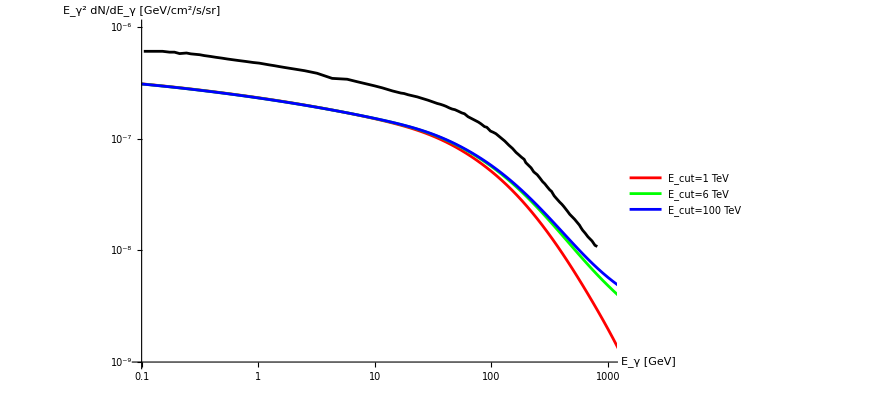

```mathematica
ListLogLogPlot[{LOSdiffuseFluxLDDEdpl[[1]],LOSdiffuseFluxLDDEdpl[[2]],LOSdiffuseFluxLDDEdpl[[3]],blazarEGB},Joined->True,PlotStyle->{Red,Green,Blue,Black},PlotLegends->Placed[{"E_cut=1 TeV","E_cut=6 TeV","E_cut=100 TeV"},{0.5,0.25}],AxesLabel->{"E_γ [GeV]","E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]"},PlotRange->{{0.1,1000},{10^-6,10^-9}}]
```

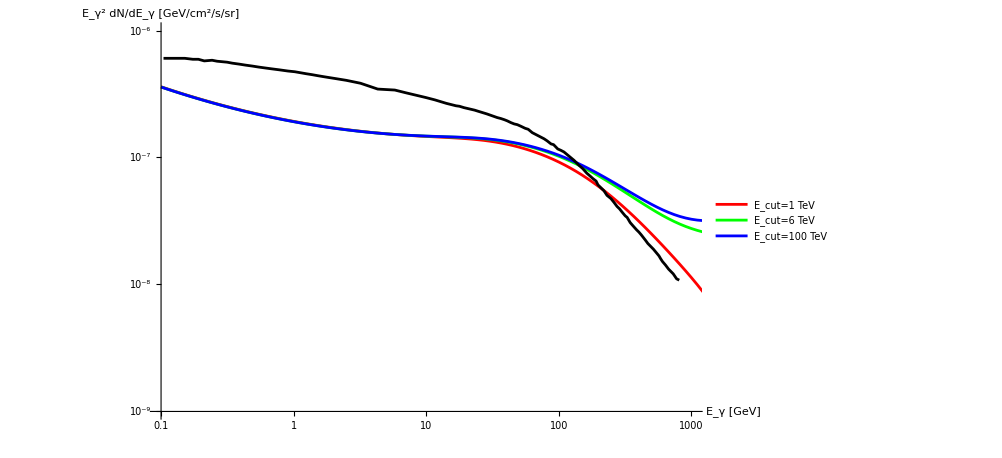

```mathematica
ListLogLogPlot[{LOSdiffuseFluxLDDEpl[[1]],LOSdiffuseFluxLDDEpl[[2]],LOSdiffuseFluxLDDEpl[[3]],blazarEGB},Joined->True,PlotStyle->{Red,Green,Blue,Black},PlotLegends->Placed[{"E_cut=1 TeV","E_cut=6 TeV","E_cut=100 TeV"},{0.5,0.25}],AxesLabel->{"E_γ [GeV]","E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]"},PlotRange->{{0.1,1000},{10^-6,10^-9}}]
```

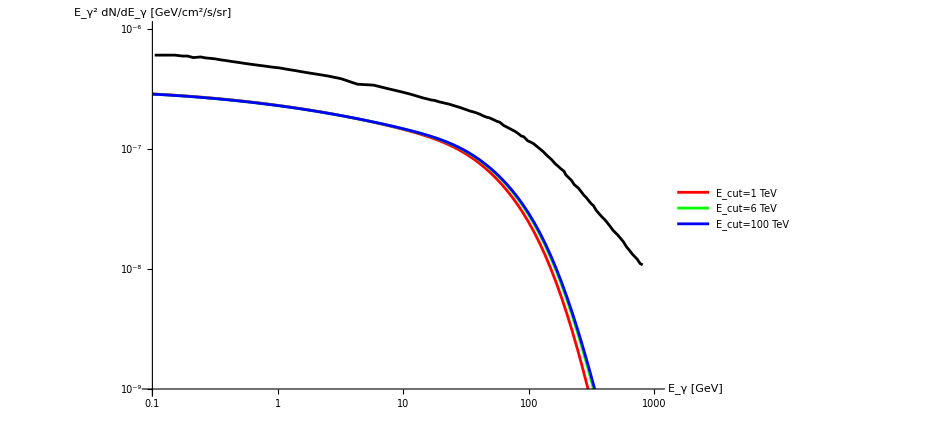

```mathematica
ListLogLogPlot[{LOSdiffuseFluxPLEdpl[[1]],LOSdiffuseFluxPLEdpl[[2]],LOSdiffuseFluxPLEdpl[[3]],blazarEGB},Joined->True,PlotStyle->{Red,Green,Blue,Black},PlotLegends->Placed[{"E_cut=1 TeV","E_cut=6 TeV","E_cut=100 TeV"},{0.5,0.25}],AxesLabel->{"E_γ [GeV]","E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]"},PlotRange->{{0.1,1000},{10^-6,10^-9}}]
```

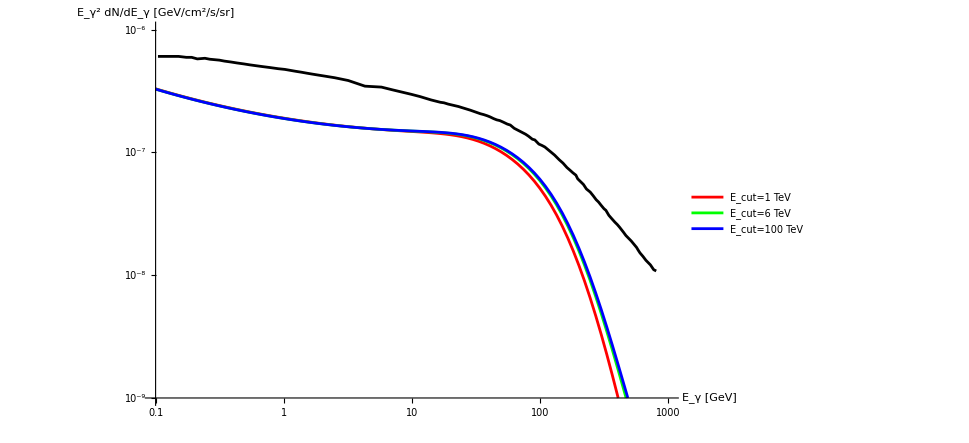

```mathematica
ListLogLogPlot[{LOSdiffuseFluxPLEpl[[1]],LOSdiffuseFluxPLEpl[[2]],LOSdiffuseFluxPLEpl[[3]],blazarEGB},Joined->True,PlotStyle->{Red,Green,Blue,Black},PlotLegends->Placed[{"E_cut=1 TeV","E_cut=6 TeV","E_cut=100 TeV"},{0.5,0.25}],AxesLabel->{"E_γ [GeV]","E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]"},PlotRange->{{0.1,1000},{10^-6,10^-9}}]
```

```mathematica
redshiftFunc[Γ_,Ecut_]:=RedshiftDiffuse[dNdEarr[Γ,Ecut],10,ρArr[Γ,Ecut]*624.151]
```

```mathematica
Γarr =Range[1,3,(3-1)/(10-1)];
EcutArr={1000,6000,100000};
redshiftFluxArr = Table[
Table[
Transpose[{energies,energies^2*redshiftFunc[i,j]}],
{i,Γarr}],
{j,EcutArr}];
CloseKernels[];
LaunchKernels[];
```

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

Injected spectrum properly formatted.

Comoving density distribution properly formatted.

```mathematica
Δγ
```

2/9

```mathematica
Δγ=Γarr[[2]]-Γarr[[1]];
redshiftFluxArrs=Table[
Transpose[{energies,Sum[(redshiftFluxArr[[j]][[i]][[All,2]]+redshiftFluxArr[[j]][[i+1]][[All,2]])/2*Δγ,{i,9}]}],
{j,3}];
diffuseRedshift=Table[
Interpolation[redshiftFluxArrs[[i]]],
{i,3}];
```

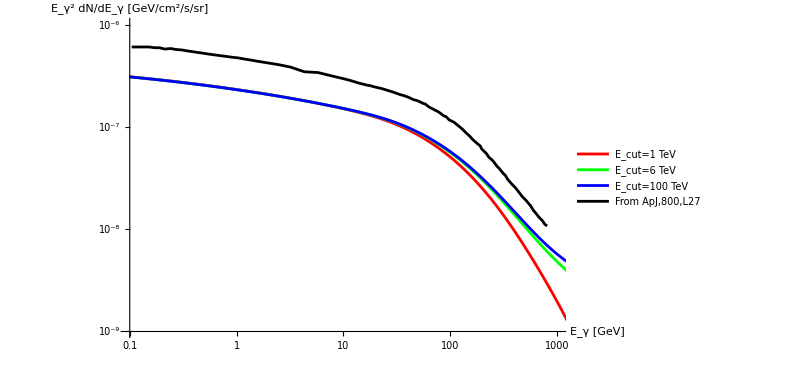

```mathematica
ListLogLogPlot[{LOSdiffuseFluxLDDEdpl[[1]],LOSdiffuseFluxLDDEdpl[[2]],LOSdiffuseFluxLDDEdpl[[3]],blazarEGB},Joined->True,PlotStyle->{Red,Green,Blue,Black},PlotLegends->Placed[{"E_cut=1 TeV","E_cut=6 TeV","E_cut=100 TeV","From ApJ,800,L27 "},{0.5,0.25}],AxesLabel->{"E_γ [GeV]","E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]"},PlotRange->{{0.1,1000},{10^-6,10^-9}}]
```

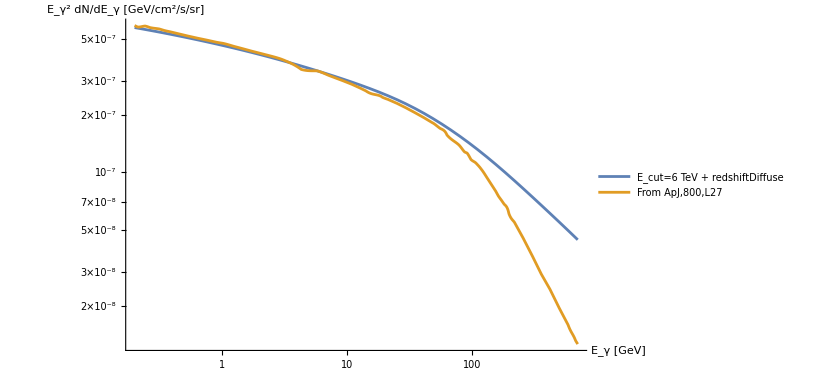

```mathematica
LogLogPlot[{LOSdiffuseFluxLDDEdpl[[2]][x]+diffuseRedshift[[2]][x],Interpolation[blazarEGB][x]},{x,0.2,700},PlotLegends->Placed[{"E_cut=6 TeV + redshiftDiffuse","From ApJ,800,L27 "},{0.5,0.25}],AxesLabel->{"E_γ [GeV]","E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]"}]
```

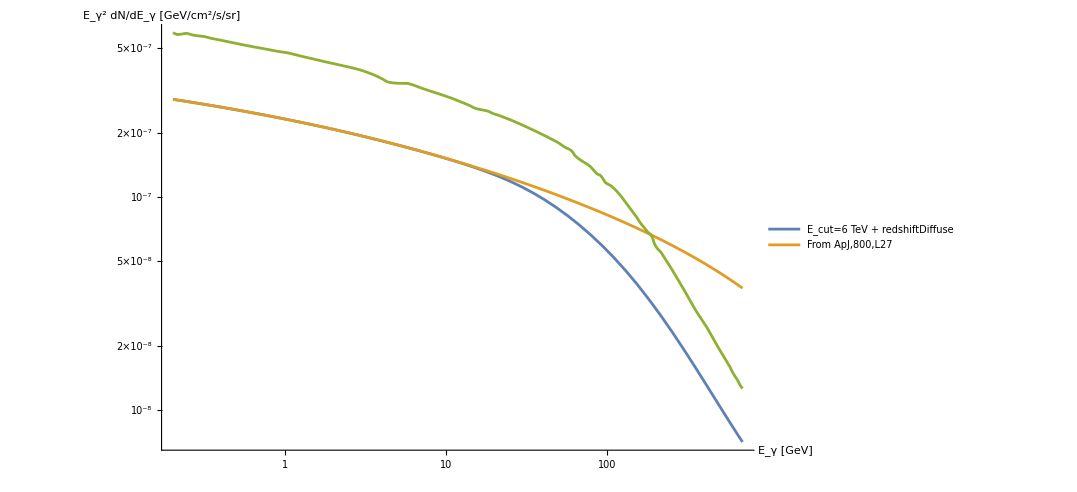

```mathematica
LogLogPlot[{LOSdiffuseFluxLDDEdpl[[2]][x],diffuseRedshift[[2]][x],Interpolation[blazarEGB][x]},{x,0.2,700},PlotLegends->Placed[{"E_cut=6 TeV + redshiftDiffuse","From ApJ,800,L27 "},{0.5,0.25}],AxesLabel->{"E_γ [GeV]","E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]"}]
```

### Taking the known components into account

```mathematica
knownPlus1LDDEdpl=Transpose[{
Take[energies,100],
Table[allKnownLower[i],{i,Take[energies,100]}]+Take[diffuseFluxArrs[[1]][[All,2]],100]-Take[LOSdiffuseFluxArrsLDDEdpl[[1]][[All,2]],100]
}];
knownPlus6LDDEdpl=Transpose[{
Take[energies,100],
Table[allKnownLower[i],{i,Take[energies,100]}]+Take[diffuseFluxArrs[[2]][[All,2]],100]-Take[LOSdiffuseFluxArrsLDDEdpl[[2]][[All,2]],100]
}];
knownPlus100LDDEdpl=Transpose[{
Take[energies,100],
Table[allKnownLower[i],{i,Take[energies,100]}]+Take[diffuseFluxArrs[[3]][[All,2]],100]-Take[LOSdiffuseFluxArrsLDDEdpl[[3]][[All,2]],100]
}];
knownPlus1LDDEpl=Transpose[{
Take[energies,100],
Table[allKnownLower[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPL[[1]][[All,2]],100]-Take[LOSdiffuseFluxArrsLDDEpl[[1]][[All,2]],100]
}];
knownPlus6LDDEpl=Transpose[{
Take[energies,100],
Table[allKnownLower[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPL[[2]][[All,2]],100]-Take[LOSdiffuseFluxArrsLDDEpl[[2]][[All,2]],100]
}];
knownPlus100LDDEpl=Transpose[{
Take[energies,100],
Table[allKnownLower[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPL[[3]][[All,2]],100]-Take[LOSdiffuseFluxArrsLDDEpl[[3]][[All,2]],100]
}];
knownPlus1PLEdpl=Transpose[{
Take[energies,100],
Table[allKnownLower[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPLEdpl[[1]][[All,2]],100]-Take[LOSdiffuseFluxArrsPLEdpl[[1]][[All,2]],100]
}];
knownPlus6PLEdpl=Transpose[{
Take[energies,100],
Table[allKnownLower[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPLEdpl[[2]][[All,2]],100]-Take[LOSdiffuseFluxArrsPLEdpl[[2]][[All,2]],100]
}];
knownPlus100PLEdpl=Transpose[{
Take[energies,100],
Table[allKnownLower[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPLEdpl[[3]][[All,2]],100]-Take[LOSdiffuseFluxArrsPLEdpl[[3]][[All,2]],100]
}];
knownPlus1PLEpl=Transpose[{
Take[energies,100],
Table[allKnownLower[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPLEpl[[1]][[All,2]],100]-Take[LOSdiffuseFluxArrsPLEpl[[1]][[All,2]],100]
}];
knownPlus6PLEpl=Transpose[{
Take[energies,100],
Table[allKnownLower[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPLEpl[[2]][[All,2]],100]-Take[LOSdiffuseFluxArrsPLEpl[[2]][[All,2]],100]
}];
knownPlus100PLEpl=Transpose[{
Take[energies,100],
Table[allKnownLower[i],{i,Take[energies,100]}]+Take[diffuseFluxArrsPLEpl[[3]][[All,2]],100]-Take[LOSdiffuseFluxArrsPLEpl[[3]][[All,2]],100]
}];
```

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.11053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.122168} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.11053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.122168} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.11053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.122168} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.11053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.122168} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.11053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.122168} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.11053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.122168} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.11053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.122168} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.11053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.122168} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.11053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.122168} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.11053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.122168} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.11053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.122168} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.11053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.122168} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

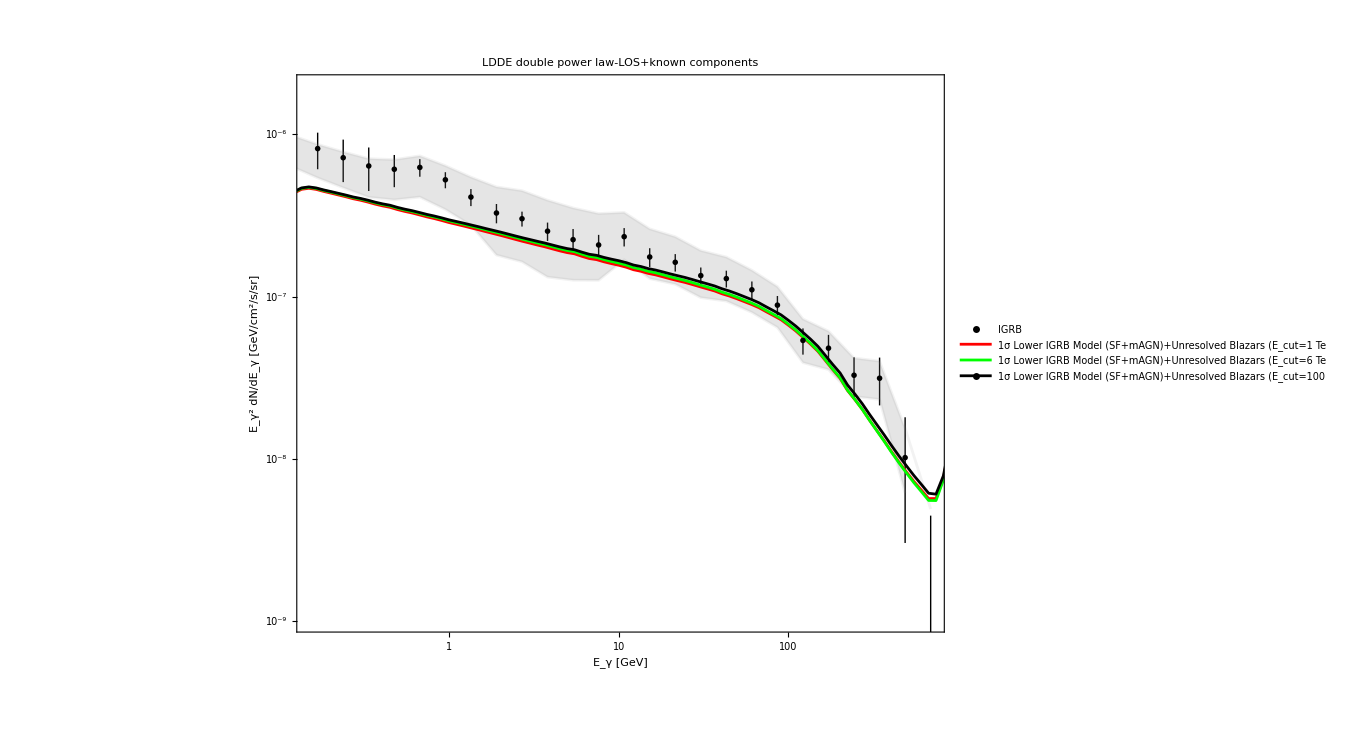

```mathematica
ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,knownPlus1LDDEdpl,knownPlus6LDDEdpl,knownPlus100LDDEdpl},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green},
PlotRange->{{0.15,700},{10^-9,2*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->20],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->20],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
PlotLabel->Style["LDDE double power law-LOS+known components",FontFamily->"Times",FontSize->25,Black],
PlotLegends->Placed[{Style["IGRB",FontFamily->"Times",FontSize->14],None,None,Style["1σ Lower IGRB Model (SF+mAGN)+Unresolved Blazars (E_cut=1 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model (SF+mAGN)+Unresolved Blazars (E_cut=6 TeV)",FontFamily->"Times",FontSize->14],Style["1σ Lower IGRB Model (SF+mAGN)+Unresolved Blazars (E_cut=100 TeV)",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

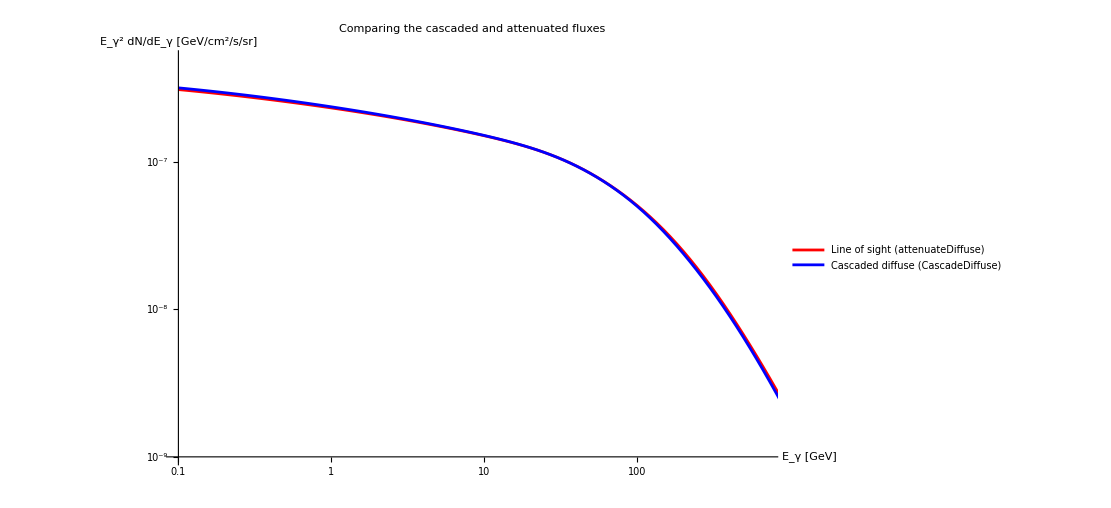

```mathematica
ListLogLogPlot[{LOSdiffuseFluxArrsLDDEdpl[[1]],diffuseFluxArrs[[1]]},Joined->True,PlotRange->{{0.1,700},{10^-9,5*10^-7}},PlotStyle->{Red,Blue},PlotLegends->{"Line of sight (attenuateDiffuse)","Cascaded diffuse (CascadeDiffuse)"},PlotLabel->"Comparing the cascaded and attenuated fluxes",
AxesLabel->{"E_γ [GeV]","E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]"}]
```

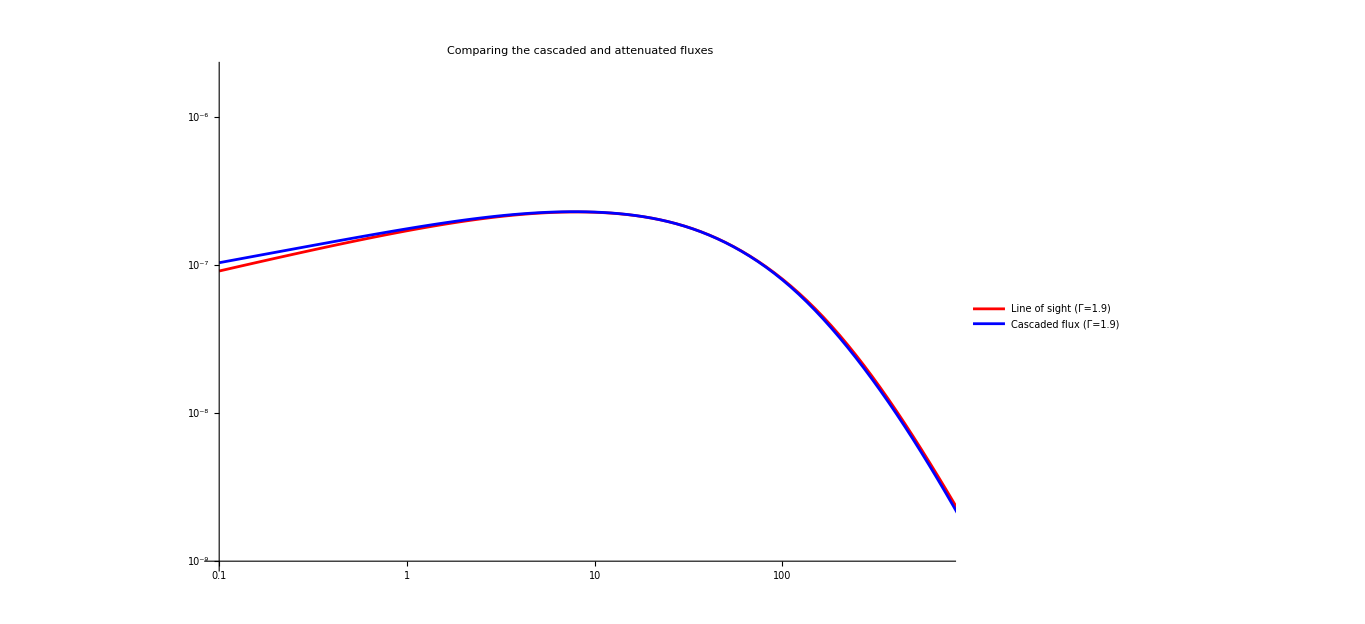

```mathematica
ListLogLogPlot[{LOSfluxArr[[1]][[5]],fluxArr[[1]][[5]]},Joined->True,PlotRange->{{0.1,700},{10^-9,2*10^-6}},PlotStyle->{Red,Blue},PlotLegends->{"Line of sight (Γ=1.9)","Cascaded flux (Γ=1.9)"},PlotLabel->"Comparing the cascaded and attenuated fluxes"]
```

```mathematica
totArr=Table[{x,SFmid[x]+mAGNmid[x]+diffuseFlux[[2]][x]},{x,logSpace[0.2,700,300]}];
knownMidArr=Import["known_components/all_mid.csv","CSV"];
```

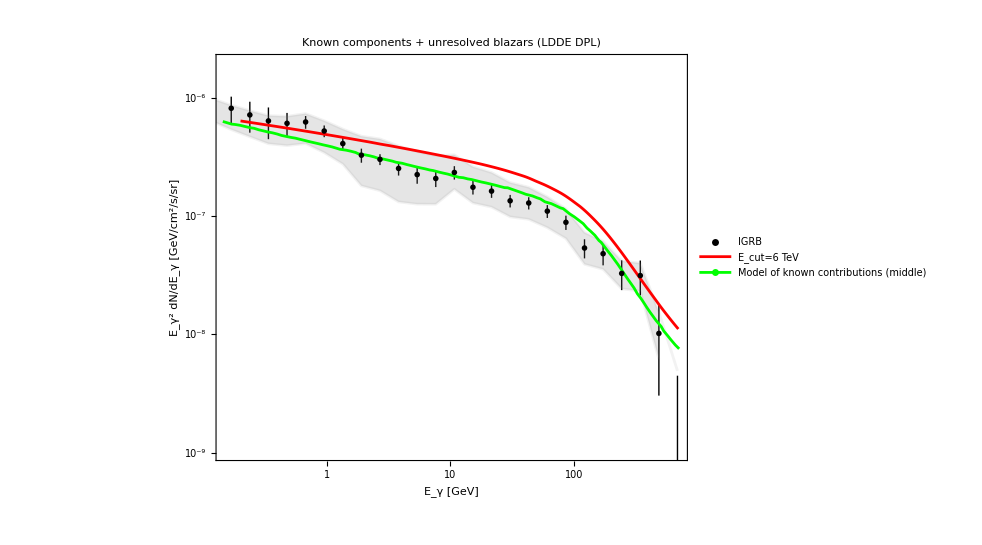

```mathematica
ListLogLogPlot[{IGRBModel,IGRBForegroundUpper,IGRBForegroundLower,totArr,knownMidArr},
Frame->True,
Joined->{False,True,True,True,True,True},
Filling->{2->{3}},
PlotStyle->{IGRBPointStyle,IGRBRangeStyle,IGRBRangeStyle,Red,Green},
PlotRange->{{0.15,700},{10^-9,2*10^-6}},
PlotMarkers->{{Automatic,Scaled[0.02]},None,None,None,None,None},
IntervalMarkersStyle->{Black},
FrameLabel->{{Style["E_γ^2 dN/dE_γ [GeV/cm^2/s/sr]",FontFamily->"Times",FontSize->20],None},{Style["E_γ [GeV]",FontFamily->"Times",FontSize->20],None}}, 
Frame->True,
AspectRatio->3/4,
FrameStyle->Black,
PlotLabel->Style["Known components + unresolved blazars (LDDE DPL)",FontFamily->"Times",FontSize->25,Black],
PlotLegends->Placed[{Style["IGRB",FontFamily->"Times",FontSize->14],None,None,Style["E_cut=6 TeV",FontFamily->"Times",FontSize->14],Style["Model of known contributions (middle)",FontFamily->"Times",FontSize->14]},{0.5,0.2}]]
```

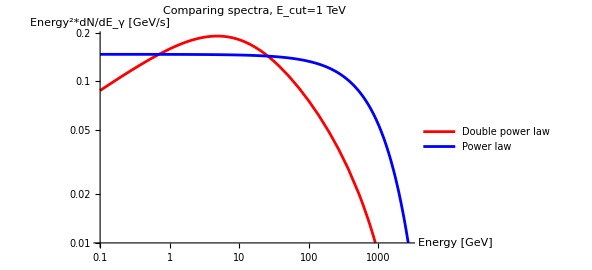

```mathematica
LogLogPlot[{En^2*dNdEnorm[En,2,1000],En^2*dNdEnormPL[En,2,1000]},{En,Min[energies],10^6},PlotLegends->Placed[{"Double power law", "Power law"}, {0.5,0.15}],PlotStyle->{Red,Blue},AxesLabel->{"Energy [GeV]","Energy^2*dN/dE_γ [GeV/s]"},PlotLabel->"Comparing spectra, E_cut=1 TeV",PlotRange->{{0.1,1000},{0.5,10^-2}}]
```

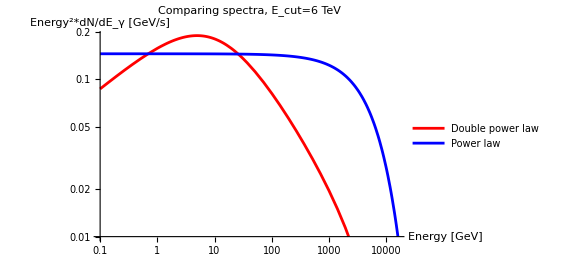

```mathematica
LogLogPlot[{En^2*dNdEnorm[En,2,6000],En^2*dNdEnormPL[En,2,6000]},{En,Min[energies],10^6},PlotLegends->Placed[{"Double power law", "Power law"}, {0.5,0.15}],PlotStyle->{Red,Blue},AxesLabel->{"Energy [GeV]","Energy^2*dN/dE_γ [GeV/s]"},PlotLabel->"Comparing spectra, E_cut=6 TeV",PlotRange->{{0.1,1000},{0.5,10^-2}}]
```

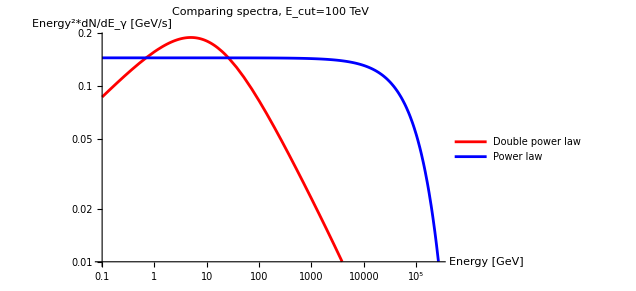

```mathematica
LogLogPlot[{En^2*dNdEnorm[En,2,100000],En^2*dNdEnormPL[En,2,100000]},{En,Min[energies],10^6},PlotLegends->Placed[{"Double power law", "Power law"}, {0.5,0.15}],PlotStyle->{Red,Blue},AxesLabel->{"Energy [GeV]","Energy^2*dN/dE_γ [GeV/s]"},PlotLabel->"Comparing spectra, E_cut=100 TeV",PlotRange->{{0.1,1000},{0.5,10^-2}}]
```

## Checking if the error is with my definition of flux

### using RedshiftPoint should get the same flux

```mathematica
fluxγ[L_?NumericQ,Γ_?NumericQ,z_?NumericQ,Ecut_]:=Block[{Print},
NIntegrate[Energy*Interpolation[Transpose[{energies,
RedshiftPoint[normDPL[L,Γ,Ecut]*Table[dNdEDPL[En,2.2,6000],{En,energies}],z]*η[Γ,z,0.1,100,Ecut]*624.151}]][Energy]
,{Energy,0.1,100}]
] //Quiet
```

```mathematica
Larr = logSpace[10^48,10^52,32];
fluxγArr= Table[{L,fluxγ[L,2.2,1,6000]},{L,Larr}];
fluxArr= Table[{L,flux[L,2.2,1,6000]},{L,Larr}];
```

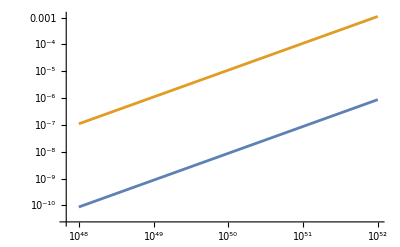

```mathematica
ListLogLogPlot[{fluxγArr,fluxArr},Joined->True]
```

InterpolatingFunction::dmval: Input value {2.14209×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.88317×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.88063×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

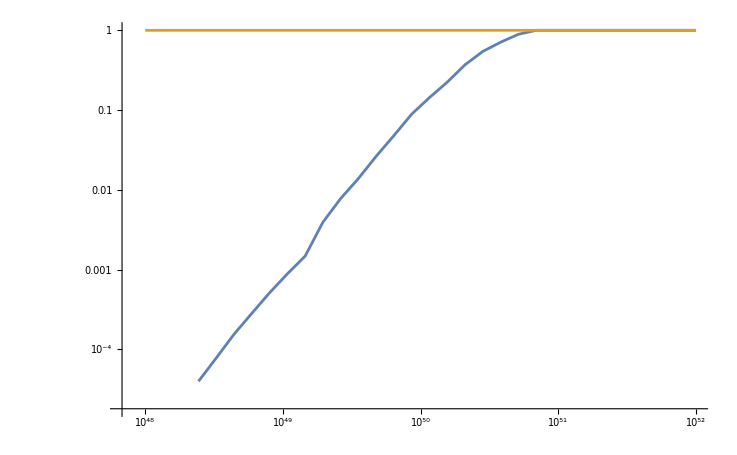

```mathematica
ListLogLogPlot[{Table[{fluxγArr[[All,1]][[i]],newFermiFunc[fluxγArr[[All,2]][[i]]]},{i,Length[fluxγArr[[All,2]]]}],Table[{fluxArr[[All,1]][[i]],newFermiFunc[fluxArr[[All,2]][[i]]]},{i,Length[fluxArr[[All,2]]]}]},Joined->True]
```

```mathematica
Lvals=logSpace[10^43,10^52,32];
Γvals=Range[1,3,(3-1)/31];
zVals = logSpace[Min@diffuseDistances,Max@diffuseDistances,32];
DistributeDefinitions[fluxγ,diffuseDistances,logSpace,Lvals,Γvals,zVals];
fluxValues=ParallelTable[{L,Γ,z,fluxγ[L,Γ,z,6000]},{L,Lvals},{Γ,Γvals},{z,zVals}];
CloseKernels[];
LaunchKernels[];
fluxInt=Interpolation[Flatten[fluxValues,2],InterpolationOrder->1] (* function of L,Γ,z*);
```

```mathematica
Larr = logSpace[10^43,10^52,32];
fluxγArr= Table[{L,fluxγ[L,1,1,6000]},{L,Larr}];
fluxIntArr= Table[{L,fluxInt[L,1,1]},{L,Larr}];
```

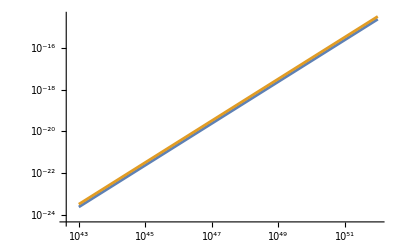

```mathematica
ListLogLogPlot[{fluxγArr,fluxIntArr},Joined->True]
```

## Correct way of calculating optical depth

### Uses eq. 46 of 2408.03995v2, the behavior of this function is not super well-defined, so I added some fixes that make the function much more smooth and easier to integrate

#### Takes small values of τ to be zero and replaces indeterminate with greatest value before it

```mathematica
fixingData[yValues_]:=Module[{adjustedValues,indIndex,maxBefore},
adjustedValues=Replace[yValues,x_/;x<10^-3->0,{1}];
indIndex=FirstPosition[yValues,Indeterminate][[1]];
maxBefore=yValues[[indIndex-1]];
ReplacePart[
adjustedValues,Thread[Range[indIndex,Length[adjustedValues]]->maxBefore]
]
]
```

#### Makes use of the fact that this function should be increasing

```mathematica
fixingDecreasing[yValues_]:=Module[{decreaseIndex,maxBefore},
decreaseIndex=FirstPosition[Differences[data[[1]][[All,3]]],x_/;x<0][[1]];
If[
decreaseIndex===Missing[],
Return[yValues],
maxBefore=yValues[[decreaseIndex]];
ReplacePart[yValues,Thread[Range[decreaseIndex+1,Length[yValues]]->maxBefore]]
]
]
```

#### Getting the values of τ

```mathematica
flatSpec=Table[1,Length[energies]];
(*Φredshift[z_]:=(1+z)^2/(4*Pi*dl[z]^2)*flatSpec*)
Φredshift[z_]:=RedshiftPoint[flatSpec,z]
Φatten[z_]:=AttenuatePoint[flatSpec,z]
tauArr[z_]:=Transpose[{energies,-Log[Φatten[z]/Φredshift[z]]}]
zValues=logSpace[Min@diffuseDistances,10,50]; 
data=Block[{Print},
Table[
With[{tauValues=tauArr[z]},Table[{tauValues[[i,1]],z,tauValues[[i,2]]},{i,1,300}]]
,{z,zValues}]
];
```

#### Fixing the data and getting τ[E_γ,z]

```mathematica
Do[
data[[i]][[All,3]]=fixingData[data[[i]][[All,3]]],{i,1,Length[data]}
] //Quiet
Do[
data[[i]][[All,3]]=fixingDecreasing[data[[i]][[All,3]]],{i,1,Length[data]}
] //Quiet

fixedData=Flatten[data,1];
tau=Evaluate@Interpolation[fixedData] (* optical depth, function of energy,z *);
expOpticalDepth[En_,z_]:=Exp[-tau[En,z]]
```

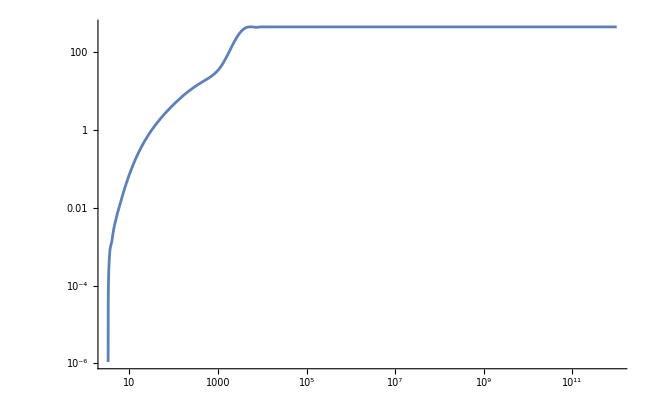

```mathematica
LogLogPlot[tau[En,5],{En,1,Max@energies},PlotRange->All]
```